This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 9 AnnularProperties ch9AnnularProperties.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Compute singular points and annular template

### Section 2.1: Compute singular points and annular template

```mathematica
(*
 compute annular table data
*)

 $implicitF[z_,w_]=$theFunction;
 {$theSingularList,argList,$zeroIndexes,$poleIndexes,$minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}=getAnnularTemplate[$theFunction];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
```

poleIndexes: {1,7,8}

Routine for singular point at zero

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 |   |   |   |   | {} |   |  
1 |   | {0.,0.223263} | 0.111631 |   |   |   | {} |   |  
  | 2 | 0.176998-0.136081 ⅈ | 0.074421 | -0.65544 |   |   | {} |   |  
  | 3 | 0.176998+0.136081 ⅈ | 0.074421 | 0.65544 |   |   | {} |   |  
2 |   | {0.223263,2.07279} | 1.14803 |   |   |   | {} |   |  
  | 4 | 2.07279 | 0.309069 | 0. |   |   | {} |   |  
3 |   | {2.07279,2.79826} | 2.43553 |   |   |   | {} |   |  
  | 5 | 0.827092-2.67323 ⅈ | 0.873038 | -1.27074 |   |   | {} |   |  
  | 6 | 0.827092+2.67323 ⅈ | 0.873038 | 1.27074 |   |   | {} |   |  
4 |   | {2.79826,3.} | 2.89913 |   |   |   | {} |   |  
  | 7 | -3. | 0.0162237 | 3.14159 |   |   | {} |   |  
  | 8 | 3. | 0.309069 | 0. |   |   | {} |   |  
5 |   | {3.,3.04039} | 3.0202 |   |   |   | {} |   |  
  | 9 | -3.04027-0.0273346 ⅈ | 0.0162237 | -3.1326 |   |   | {} |   |  
  | 10 | -3.04027+0.0273346 ⅈ | 0.0162237 | 3.1326 |   |   | {} |   |  
6 |   | {3.04039,6.0783} | 4.55935 |   |   |   | {} |   |  
  | 11 | -5.00022-3.45595 ⅈ | 1.31643 | -2.53682 |   |   | {} |   |  
  | 12 | -5.00022+3.45595 ⅈ | 1.31643 | 2.53682 |   |   | {} |   |  
7 |   | {6.0783,10.0783} | 8.0783 |   |   |   | {} |   |

### Section 2.2: Import annular table with monodromies and continuation graphics if available (not needed for this notebook)

```mathematica
(*
 import annular table for calcuations
*)
If[FileExistsQ[annularTableWithMonodromiesFileName[$theTestCase]],
{annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
annularResidueTable={#[[1]],#[[2]],#[[3]],#[[6]]}&/@ annulusTableR;
annularResidueReport=Prepend[annularResidueTable,{"a_n Index","s_n Index","a_n or s_n","Monodromy"}];

monodromyGridReport=Style[Labeled[Grid[annularResidueReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold,Black],Top],10];
Print[monodromyGridReport];
,
Print[Style["annular table with monodromies not found",Red]];
];
(*
 import figure of branch links
*)
If[FileExistsQ[annularTableWithBranchLinksFileName[$theTestCase]],
annularLinkTable=Import[annularTableWithBranchLinksFileName[$theTestCase]];
Print[Show[annularLinkTable,ImageSize->800]];
,
Print[Style["Annular table with branch links file not found",Red]];
];

(* {annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];*)
 (*{annulusTable,annulusTableR,annulusTableReport}=Import[annularMonodromyTableFileName[$theTestCase]];*)
(*annulusTableReport//N//MatrixForm 
*)
maxAnnulus=annulusTable[[-1,1]];
```

annular table with monodromies not found

Annular table with branch links file not found

## Section 3: Compute pole data

### Section 3.1: Compute poles, pole perimeters and illustrate poles

Pole indexes: {1,7,8}

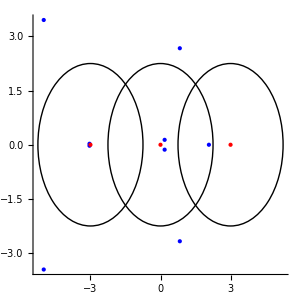

```mathematica
(*
 generate polar perimters 
*)
 Print["Pole indexes: ",$poleIndexes];
If[Length@$poleIndexes>1,
nearestPole=(NearestTo[#1,2][$theSingularList[[$poleIndexes]]]&/@ $theSingularList[[$poleIndexes]])[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{$theSingularList[[$poleIndexes]],nearestPole}];
poleRadiusArray=MapThread[3/4Abs[#1-#2]&,{$theSingularList[[$poleIndexes]],nearestPole}];
 theSings=$theSingularList;
thePoles=$theSingularList[[$poleIndexes]];
theRingList=Abs[#]&/@ theSings;
maxX=Abs[$theSingularList[[-1]]]+2;
maxX=theAnnuli[[-1,2]];

nonPoleIndexes=Complement[Range[1,Length@$theSingularList],$poleIndexes];

singG=Graphics@{PointSize[0.01],Blue,Point@(ReIm@#&/@ $theSingularList[[nonPoleIndexes]])};
poleG=Graphics@{PointSize[.01],Red,Point@(ReIm@#&/@ thePoles)};
polePerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{$theSingularList[[$poleIndexes]],poleRadiusArray}];

(*circleX=Graphics@{Red,Circle[{2,-2},2Sqrt[2]]};*)
envelopeCircle=Graphics@Circle[{0,0},maxX];

Print@Show[{singG,poleG,polePerimetersG (*,envelopeCircle*)(*,circleX*)},Axes->True,AspectRatio->1,PlotRange->maxX,ImageSize->300];
,
maxX=theAnnuli[[-1,2]];
poleRadiusArray={maxX};
 theSings=$theSingularList;
envelopeCircle=Graphics@Circle[{0,0},maxX];

thePoles=$theSingularList[[$poleIndexes]];
singG=Graphics@{PointSize[0.05],Blue,Point@(ReIm@#&/@ theSings)};
poleG=Graphics@{PointSize[.025],Red,Point@(ReIm@#&/@ thePoles)};
polePerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{$theSingularList[[$poleIndexes]],poleRadiusArray}];
Print@Show[{singG,poleG,polePerimetersG,envelopeCircle(*,circleX*)},Axes->True,AspectRatio->1,PlotRange->maxX,ImageSize->300];
];
```

### Section 3.2: Get pole residues

```mathematica
poleFlag=True;
 For[i=1,i<=Length@$poleIndexes,i++,
If[!FileExistsQ@seriesFileName[$theTestCase,$poleIndexes[[i]]],
Print[Style["Pole expansion file "<>seriesFileName[$theTestCase,$poleIndexes[[i]]]<>" not found",Red]];
poleFlag=False;
];
]

If[poleFlag,
runningResidueSum=0;
poleResidueTable=Table[
 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,$poleIndexes[[pIndex]]],
dataList=Import[seriesFileName[$theTestCase,$poleIndexes[[pIndex]]]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
(*
 search for residue
*)
residueList=(Coefficient[#,z,-1]&/@ baseSeries);
residueSum=Plus@@residueList;
runningResidueSum+=residueSum;
,
Print["File not found!"];
Abort[];
];
poleContourF[z_]:=$theSingularList[[$poleIndexes[[pIndex]]]]+poleRadiusArray[[pIndex]] Exp[I t];

{$poleIndexes[[pIndex]],Select[residueList,Abs[#]>10^-150&],residueSum,runningResidueSum,poleRadiusArray[[pIndex]],poleContourF[t]},
{pIndex,1,Length@$poleIndexes}
];
Print["Length of baseSeries: ",Length@baseSeries[[1]]];

 poleResidueTableReport={#[[1]],N[#[[2]]],N[#[[3]]],N[#[[4]]],N[#[[5]]],N[#[[6]]]}&/@ poleResidueTable;
Print[Style[Grid[Prepend[poleResidueTableReport,{"Pole index","Residues","Sum","Running sum","Radius","Contour"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}],8]]
Precision@poleResidueTable[[All,4]]
];
```

Length of baseSeries: 256

Pole index | Residues | Sum | Running sum | Radius | Contour
1 | {0.777778} | 0.777778 | 0.777778 | 2.25 | 2.25 2.71828^((0.+1. ⅈ) t)
7 | {-0.222222} | -0.222222 | 0.555556 | 2.25 | -3.+2.25 2.71828^((0.+1. ⅈ) t)
8 | {3.44444} | 3.44444 | 4. | 2.25 | 3.+2.25 2.71828^((0.+1. ⅈ) t)

#### Additional code for testCase0022

```mathematica
theSingularIndex=1;
pos=Position[poleResidueTable[[All,1]],x_/;x==theSingularIndex]

If[Length@pos==0,
Print["Pole ",theSingularIndex," not in residueData table"];
Abort[];
,
residueDataIndex=pos[[1,1]];
poleMaxRadius=poleResidueTable[[residueDataIndex,5]]//N;
asyResidues=asyPoleTable[[residueDataIndex]];
Print["asyResidues: ",asyResidues];
dataList=Import[seriesFileName[$theTestCase,theSingularIndex]];
Print["Base series: "];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
Print[Style[baseSeries[[All,1;;6]]//N//MatrixForm,8]];
];
Length@baseSeries[[1]]
```

{{1}}

asyResidues: {-8,-8,-8,-8}

Base series:

(-5.33333-11.3333/z^(3/2)-8./z-7.55556/(√z)-(0.+2. ⅈ)/z^(1/4)+(0.+14.6667 ⅈ) z^(1/4)
-5.33333+11.3333/z^(3/2)-8./z+7.55556/(√z)-2./z^(1/4)-14.6667 z^(1/4)
-5.33333-11.3333/z^(3/2)-8./z-7.55556/(√z)+(0.+2. ⅈ)/z^(1/4)-(0.+14.6667 ⅈ) z^(1/4)
-5.33333+11.3333/z^(3/2)-8./z+7.55556/(√z)+2./z^(1/4)+14.6667 z^(1/4))

515

```mathematica
Style[baseSeries[[1;;4,1;;5]]//N//MatrixForm,10]
Style[baseSeries[[5;;8,1;;5]]//N//MatrixForm,10]
Style[baseSeries[[9;;12,1;;5]]//N//MatrixForm,10]
```

((-0.666667-0.25 ⅈ)-(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z+(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)+(0.244276-0.2799 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z+(0.0906903-0.012384 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z
(-0.666667-0.25 ⅈ)-(0.244276-0.2799 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z-(0.0906903-0.012384 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z)

((0.666667+0.25 ⅈ)-(0.2799+0.244276 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z+(0.012384+0.0906903 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)+(0.244276-0.2799 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z+(0.0906903-0.012384 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)-(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z
(0.666667+0.25 ⅈ)-(0.244276-0.2799 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.0906903-0.012384 ⅈ) z^(3/4)-(0.00770177-0.0339537 ⅈ) z)

(-1.9726/z^(1/4)-(0.5598+0.488553 ⅈ) z^(1/4)+(0.0247681+0.181381 ⅈ) z^(3/4)+(0.0426432-0.0648286 ⅈ) z^(5/4)-(0.0324034-0.00901773 ⅈ) z^(7/4)
(0.+1.9726 ⅈ)/z^(1/4)+(0.488553-0.5598 ⅈ) z^(1/4)+(0.181381-0.0247681 ⅈ) z^(3/4)+(0.0648286+0.0426432 ⅈ) z^(5/4)+(0.00901773+0.0324034 ⅈ) z^(7/4)
1.9726/z^(1/4)+(0.5598+0.488553 ⅈ) z^(1/4)-(0.0247681+0.181381 ⅈ) z^(3/4)-(0.0426432-0.0648286 ⅈ) z^(5/4)+(0.0324034-0.00901773 ⅈ) z^(7/4)
-(0.+1.9726 ⅈ)/z^(1/4)-(0.488553-0.5598 ⅈ) z^(1/4)-(0.181381-0.0247681 ⅈ) z^(3/4)-(0.0648286+0.0426432 ⅈ) z^(5/4)-(0.00901773+0.0324034 ⅈ) z^(7/4))

#### Convert fractional Puiseux series to latex format

```mathematica
baseBranchTypeArray
 (*coefRules=getCoefficientRulesC[baseSeries[[1,1;;5]]//N,3];
theKeys=Keys[coefRules];
theValues=Values[coefRules];*)
seriesString="";
jStart=5;
jEnd=8;
For[j=jStart,j<=jEnd,j++,
 coefRules=getCoefficientRulesC[baseSeries[[j,1;;5]]//N,3];
theKeys=Keys[coefRules];
theValues=Values[coefRules];
string="";
For[i=1,i<=Length@theKeys,i++,
num=Numerator[theKeys[[i]]];
den=Denominator[theKeys[[i]]];
If[i==1,
If[den!=1,
string="("<>ToString[theValues[[i]]]<>")"<>"z^{"<>ToString[num]<>"/"<>ToString[den]<>"}";
,
If[num!=1 ,
If[num!=0,
string="("<>ToString[theValues[[i]]]<>")"<>"z^{"<>ToString[num]<>"}";
,
string="("<>ToString[theValues[[i]]]<>")";
];
,
If[num!=0,
string="("<>ToString[theValues[[i]]]<>")"<>"z";
,
string="("<>ToString[theValues[[i]]]<>")";
];
];
];
,
(* i!=1 *)
If[den!=1,
string=string<>"+("<>ToString[theValues[[i]]]<>")"<>"z^{"<>ToString[num]<>"/"<>ToString[den]<>"}";
,
If[num!=1 ,
string=string<>"+("<>ToString[theValues[[i]]]<>")"<>"z^{"<>ToString[num]<>"}";
,
string=string<>"+("<>ToString[theValues[[i]]]<>")z";
];
];
];
];
string=StringReplace[string,"I"->"i"];
seriesString=seriesString<>string<>"\\\\";
];
seriesString
```

{{1V_4^1,{1,2,3,4}},{2V_4^1,{5,6,7,8}},{P_4^-1,{9,10,11,12}}}

(0.667 + 0.250 i)+(-0.280 - 0.244 i)z^{1/4}+(-0.018 - 0.033 i)z^{1/2}+(0.012 + 0.091 i)z^{3/4}+(-0.008 + 0.034 i)z\\(0.667 + 0.250 i)+(0.244 - 0.280 i)z^{1/4}+(0.018 + 0.033 i)z^{1/2}+(0.091 - 0.012 i)z^{3/4}+(-0.008 + 0.034 i)z\\(0.667 + 0.250 i)+(0.280 + 0.244 i)z^{1/4}+(-0.018 - 0.033 i)z^{1/2}+(-0.012 - 0.091 i)z^{3/4}+(-0.008 + 0.034 i)z\\(0.667 + 0.250 i)+(-0.244 + 0.280 i)z^{1/4}+(0.018 + 0.033 i)z^{1/2}+(-0.091 + 0.012 i)z^{3/4}+(-0.008 + 0.034 i)z\\

```mathematica
coefRules=getCoefficientRulesB[baseSeries[[1;;4,1;;5]]//N];
theKeys=Keys[coefRules];
theValues=Values[coefRules]//N
cList1=MapThread[Flatten@{#1,SetAccuracy[#2,3]}&,{Range[4],theValues}]
grid1=Grid[Prepend[cList1,{"Num","0","1/4","1/2","3/4","1"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
```

{{-0.666667-0.25 ⅈ,-0.2799-0.244276 ⅈ,0.0176408+0.032719 ⅈ,0.012384+0.0906903 ⅈ,0.00770177-0.0339537 ⅈ},{-0.666667-0.25 ⅈ,0.244276-0.2799 ⅈ,-0.0176408-0.032719 ⅈ,0.0906903-0.012384 ⅈ,0.00770177-0.0339537 ⅈ},{-0.666667-0.25 ⅈ,0.2799+0.244276 ⅈ,0.0176408+0.032719 ⅈ,-0.012384-0.0906903 ⅈ,0.00770177-0.0339537 ⅈ},{-0.666667-0.25 ⅈ,-0.244276+0.2799 ⅈ,-0.0176408-0.032719 ⅈ,-0.0906903+0.012384 ⅈ,0.00770177-0.0339537 ⅈ}}

{{1,-0.67-0.25 ⅈ,-0.28-0.24 ⅈ,0.02+0.03 ⅈ,0.01+0.091 ⅈ,0.008-0.03 ⅈ},{2,-0.67-0.25 ⅈ,0.24-0.28 ⅈ,-0.02-0.03 ⅈ,0.091-0.01 ⅈ,0.008-0.03 ⅈ},{3,-0.67-0.25 ⅈ,0.28+0.24 ⅈ,0.02+0.03 ⅈ,-0.01-0.091 ⅈ,0.008-0.03 ⅈ},{4,-0.67-0.25 ⅈ,-0.24+0.28 ⅈ,-0.02-0.03 ⅈ,-0.091+0.01 ⅈ,0.008-0.03 ⅈ}}

Num | 0 | 1/4 | 1/2 | 3/4 | 1
1 | -0.67-0.25 ⅈ | -0.28-0.24 ⅈ | 0.02+0.03 ⅈ | 0.01+0.091 ⅈ | 0.008-0.03 ⅈ
2 | -0.67-0.25 ⅈ | 0.24-0.28 ⅈ | -0.02-0.03 ⅈ | 0.091-0.01 ⅈ | 0.008-0.03 ⅈ
3 | -0.67-0.25 ⅈ | 0.28+0.24 ⅈ | 0.02+0.03 ⅈ | -0.01-0.091 ⅈ | 0.008-0.03 ⅈ
4 | -0.67-0.25 ⅈ | -0.24+0.28 ⅈ | -0.02-0.03 ⅈ | -0.091+0.01 ⅈ | 0.008-0.03 ⅈ

```mathematica
coefRules=getCoefficientRulesB[baseSeries[[5;;8,1;;5]]//N];
theKeys=Keys[coefRules];
theValues=Values[coefRules]//N
cList2=MapThread[Flatten@{#1,SetAccuracy[#2,3]}&,{Range[4],theValues}]
grid2=Grid[cList2,Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
```

{{0.666667+0.25 ⅈ,-0.2799-0.244276 ⅈ,-0.0176408-0.032719 ⅈ,0.012384+0.0906903 ⅈ,-0.00770177+0.0339537 ⅈ},{0.666667+0.25 ⅈ,0.244276-0.2799 ⅈ,0.0176408+0.032719 ⅈ,0.0906903-0.012384 ⅈ,-0.00770177+0.0339537 ⅈ},{0.666667+0.25 ⅈ,0.2799+0.244276 ⅈ,-0.0176408-0.032719 ⅈ,-0.012384-0.0906903 ⅈ,-0.00770177+0.0339537 ⅈ},{0.666667+0.25 ⅈ,-0.244276+0.2799 ⅈ,0.0176408+0.032719 ⅈ,-0.0906903+0.012384 ⅈ,-0.00770177+0.0339537 ⅈ}}

{{1,0.67+0.25 ⅈ,-0.28-0.24 ⅈ,-0.02-0.03 ⅈ,0.01+0.091 ⅈ,-0.008+0.03 ⅈ},{2,0.67+0.25 ⅈ,0.24-0.28 ⅈ,0.02+0.03 ⅈ,0.091-0.01 ⅈ,-0.008+0.03 ⅈ},{3,0.67+0.25 ⅈ,0.28+0.24 ⅈ,-0.02-0.03 ⅈ,-0.01-0.091 ⅈ,-0.008+0.03 ⅈ},{4,0.67+0.25 ⅈ,-0.24+0.28 ⅈ,0.02+0.03 ⅈ,-0.091+0.01 ⅈ,-0.008+0.03 ⅈ}}

1 | 0.67+0.25 ⅈ | -0.28-0.24 ⅈ | -0.02-0.03 ⅈ | 0.01+0.091 ⅈ | -0.008+0.03 ⅈ
2 | 0.67+0.25 ⅈ | 0.24-0.28 ⅈ | 0.02+0.03 ⅈ | 0.091-0.01 ⅈ | -0.008+0.03 ⅈ
3 | 0.67+0.25 ⅈ | 0.28+0.24 ⅈ | -0.02-0.03 ⅈ | -0.01-0.091 ⅈ | -0.008+0.03 ⅈ
4 | 0.67+0.25 ⅈ | -0.24+0.28 ⅈ | 0.02+0.03 ⅈ | -0.091+0.01 ⅈ | -0.008+0.03 ⅈ

```mathematica
joinList=Join[cList1,cList2];
grid1=Grid[Prepend[joinList,{"Num","0","1/4","1/2","3/4","1"}],Alignment->Center,Dividers->{{{True}},{True,True,False,False,False,True,{False},True}}]
```

Num | 0 | 1/4 | 1/2 | 3/4 | 1
1 | -0.67-0.25 ⅈ | -0.28-0.24 ⅈ | 0.02+0.03 ⅈ | 0.01+0.091 ⅈ | 0.008-0.03 ⅈ
2 | -0.67-0.25 ⅈ | 0.24-0.28 ⅈ | -0.02-0.03 ⅈ | 0.091-0.01 ⅈ | 0.008-0.03 ⅈ
3 | -0.67-0.25 ⅈ | 0.28+0.24 ⅈ | 0.02+0.03 ⅈ | -0.01-0.091 ⅈ | 0.008-0.03 ⅈ
4 | -0.67-0.25 ⅈ | -0.24+0.28 ⅈ | -0.02-0.03 ⅈ | -0.091+0.01 ⅈ | 0.008-0.03 ⅈ
1 | 0.67+0.25 ⅈ | -0.28-0.24 ⅈ | -0.02-0.03 ⅈ | 0.01+0.091 ⅈ | -0.008+0.03 ⅈ
2 | 0.67+0.25 ⅈ | 0.24-0.28 ⅈ | 0.02+0.03 ⅈ | 0.091-0.01 ⅈ | -0.008+0.03 ⅈ
3 | 0.67+0.25 ⅈ | 0.28+0.24 ⅈ | -0.02-0.03 ⅈ | -0.01-0.091 ⅈ | -0.008+0.03 ⅈ
4 | 0.67+0.25 ⅈ | -0.24+0.28 ⅈ | 0.02+0.03 ⅈ | -0.091+0.01 ⅈ | -0.008+0.03 ⅈ

```mathematica
coefRules=getCoefficientRulesB[baseSeries[[9;;12,1;;5]]//N];
theKeys=Keys[coefRules];
theValues=Values[coefRules]//N
cList3=MapThread[Flatten@{#1,SetAccuracy[#2,3]}&,{Range[4],theValues}]
grid3=Grid[Prepend[cList3,{"Num","-1/4","3/4","5/4","7/4","9/4"}],Alignment->Center,Dividers->{{{True}},{True,True,False,False,False,True,{False},True}}]
```

{{-1.9726,-0.5598-0.488553 ⅈ,0.0247681+0.181381 ⅈ,0.0426432-0.0648286 ⅈ,-0.0324034+0.00901773 ⅈ},{0.+1.9726 ⅈ,0.488553-0.5598 ⅈ,0.181381-0.0247681 ⅈ,0.0648286+0.0426432 ⅈ,0.00901773+0.0324034 ⅈ},{1.9726,0.5598+0.488553 ⅈ,-0.0247681-0.181381 ⅈ,-0.0426432+0.0648286 ⅈ,0.0324034-0.00901773 ⅈ},{0.-1.9726 ⅈ,-0.488553+0.5598 ⅈ,-0.181381+0.0247681 ⅈ,-0.0648286-0.0426432 ⅈ,-0.00901773-0.0324034 ⅈ}}

{{1,-1.97,-0.56-0.49 ⅈ,0.02+0.18 ⅈ,0.04-0.06 ⅈ,-0.03+0.009 ⅈ},{2,0.+1.97 ⅈ,0.49-0.56 ⅈ,0.18-0.02 ⅈ,0.06+0.04 ⅈ,0.009+0.03 ⅈ},{3,1.97,0.56+0.49 ⅈ,-0.02-0.18 ⅈ,-0.04+0.06 ⅈ,0.03-0.009 ⅈ},{4,0.-1.97 ⅈ,-0.49+0.56 ⅈ,-0.18+0.02 ⅈ,-0.06-0.04 ⅈ,-0.009-0.03 ⅈ}}

Num | -1/4 | 3/4 | 5/4 | 7/4 | 9/4
1 | -1.97 | -0.56-0.49 ⅈ | 0.02+0.18 ⅈ | 0.04-0.06 ⅈ | -0.03+0.009 ⅈ
2 | 0.+1.97 ⅈ | 0.49-0.56 ⅈ | 0.18-0.02 ⅈ | 0.06+0.04 ⅈ | 0.009+0.03 ⅈ
3 | 1.97 | 0.56+0.49 ⅈ | -0.02-0.18 ⅈ | -0.04+0.06 ⅈ | 0.03-0.009 ⅈ
4 | 0.-1.97 ⅈ | -0.49+0.56 ⅈ | -0.18+0.02 ⅈ | -0.06-0.04 ⅈ | -0.009-0.03 ⅈ

### Use AsymptoticSolve to compute exact residues

```mathematica
AsymptoticSolve[$implicitF[z,w]==0,w,{z,$theSingularList[[1]],5}]//N//MatrixForm
```

(w→0.111111 z^2-0.345679 z^3-0.174211 z^4-0.0403902 z^5
w→1.28571-1.07164 z+2.92571 z^2-9.55058 z^3+36.865 z^4-155.724 z^5
w→-0.5/z^3+0.5/z
w→-0.642857+(0.+1.32288 ⅈ)/(√z)+(0.+0.468599 ⅈ) √z+0.535818 z-(0.+0.202707 ⅈ) z^(3/2)+0.231587 z^2+(0.+3.83262 ⅈ) z^(5/2)+4.94813 z^3-(0.+8.65967 ⅈ) z^(7/2)-14.8454 z^4
w→-0.642857-(0.+1.32288 ⅈ)/(√z)-(0.+0.468599 ⅈ) √z+0.535818 z+(0.+0.202707 ⅈ) z^(3/2)+0.231587 z^2-(0.+3.83262 ⅈ) z^(5/2)+4.94813 z^3+(0.+8.65967 ⅈ) z^(7/2)-14.8454 z^4)

## Section 4: Study of annular property 9.3.1: A branch integral is equal to 2Pi I times the sum of the the branch residues with cyclic multiplicity

### Notebook section 4.1: Get annular integrations

```mathematica
property931UserMenu=Labeled[Column[{Row[{Style["Annular Index:",Black,Bold],Spacer[5],InputField[Dynamic@$property921Annulus,FieldSize->2],Spacer[12],Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$property921Precision,FieldSize->10]}](*,
Row[{Style["Plot type: ",Black,Bold],RadioButtonBar[Dynamic[$plotType],{Re,Im}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}]*)
},Frame->True,FrameStyle->Thick],Style["User menu for annular property 9.3.1",Bold,Black],Top]
```

Annular Index:Precision:User menu for annular property 9.3.1

```mathematica
(*
 routine to check annular property 9.2.2
*)

(*
Options[getAnnularIntegrations]={"ndSolveWP"->MachinePrecision,"intWP"->MachinePrecision,"polish"->False,"polishPrec"->50};
*)
doPolishFlag=True;
If[doPolishFlag,
integralData=getAnnularIntegrations[annulusTable,$property921Annulus,"ndSolveWP"->$property921Precision,"polish"->True,"polishPrec"->$property921Precision,"accGoal"->$property921Precision/2];
,
integralData=getAnnularIntegrations[annulusTable,$property921Annulus];
];
integralResult=Plus@@integralData;
Print["Integral accuracy: ",Accuracy@integralResult];
maxAnnulus=annulusTable[[-1,1]];
Print["integralData: ",integralData//N//MatrixForm]
Print["Sum of branch integrals: ",integralResult//N]
```

selectedMonodromies: {{1,2,3}}

Analyzing branch: {1,2,3}

Precision of NDSolve solution: 30.

Integral accuracy: 29.311

integralData: (-4.93612×10^-28+4.88692 ⅈ)

Sum of branch integrals: -4.93612×10^-28+4.88692 ⅈ

### Notebook section 9.4.2: Compute branch residual term

```mathematica
(* theAnnulusTable=annulusTable;*)
(*
 the medial contour and integration precision may require adjusting to avoid errors
*)

If[1<=$property921Annulus<=Length@theAnnuli,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,$property921Annulus];
selectedMonodromyList=annulusTable[[aIndex,6]];
branchData=Table[
selectedBranch=selectedMonodromyList[[monodromyIndex]];
selectedBranchSize=Length@selectedMonodromyList[[monodromyIndex]];
Print["Analyzing annular index ",$property921Annulus," branch ",selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

(*theAnnulus=annulusTable[[aIndex,3]];*)

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-$property921Precision];


{tStart,tEnd,rNorm,lowPrecMedialSol,selectedBranchSize}=generateMedialContour[annulusTable,$property921Annulus,monodromyIndex,$property921Precision,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)
 numPart=2;
t0=$thetaV;
t1=t0+2 Pi selectedBranchSize;
intervalArray=Array[#&,numPart+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={-selectedBranchSize};

finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t]+I Sin[t]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->$property921Precision,AccuracyGoal->$property921Precision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
coef=rNorm/(2 Pi selectedBranchSize)finalIntVal;

{integralData[[monodromyIndex]],coef,2 π ⅈ selectedBranchSize coef},
{monodromyIndex,1,Length@selectedMonodromyList}
];
,
Print["Annulus index out of range"]
]
Print["branchData: ", branchData//N//MatrixForm];
Print["Sum of branch integrals: ",integralResult//N]
Print["2PiI times sum of residues: ", branchData[[1,-1]]]
```

Analyzing annular index 2 branch {1,2,3}

Annulus: {0.223263,2.07279}

tStart: 0.523599

tEnd: 19.3732

Setting rNorm: 1.14803

tStart: 0.523599

tEnd: 19.3732

medialSol: -0.78776-1.13896 ⅈ

prec: 30.

branchData: (-4.93612×10^-28+4.88692 ⅈ | 0.259259-5.02674×10^-25 ⅈ | 9.47517×10^-24+4.88692 ⅈ)

Sum of branch integrals: -4.93612×10^-28+4.88692 ⅈ

2PiI times sum of residues: 9.47517×10^-24+4.8869219055841228153863341315 ⅈ

#### Format the color-coded error report

```mathematica
exactVal=2 Pi I 7/9; 
theResidueSum=branchData[[1,-1]];
 latexErrorString=colorAccuracyReport3[exactVal,integralResult,theResidueSum,Im,50,"actual val","Branch integral","2nPiI c_-n:"]
```

actual val | 4.886921905584122815386334151768115597640041287916i
Branch integral | 4.886921905584122815386334151280046811038655382756i
2nPiI c_-n: | 4.886921905584122815386334131470007972399797958992i

Total accurate digits: 27

{\begin{array}{cl}\text{Actual val:}&\texttt{4.886921905584122815386334151768115597640041287916i}\\\text{Integral val:}&\texttt{4.886921905584122815386334151}\color{red}\texttt{280046811038655382756i}\\\end{array},\text{second val: }&\texttt{4.8869219055841228153863341}\color{red}\texttt{31470007972399797958992}

## Section 5: Annular property 9.3.2: The sum of the branch integrals is equal to 2Pi I times the sum of the the enclosed polar residues counted with cyclic multiplicity

```mathematica
monodromyGridReport
```

a_n Index | s_n Index | a_n or s_n | Monodromy
  | 1 | 0 | {{2},{1},{3}}
1 |   | {0.,0.223263} | {{1},{2},{3}}
  | 2 | 0.176998-0.136081 ⅈ | {{1},{2,3}}
  | 3 | 0.176998+0.136081 ⅈ | {{1},{2,3}}
2 |   | {0.223263,2.07279} | {{1,2,3}}
  | 4 | 2.07279 | {{1,2},{3}}
3 |   | {2.07279,2.79826} | {{1,3},{2}}
  | 5 | 0.827092-2.67323 ⅈ | {{1},{3,2}}
  | 6 | 0.827092+2.67323 ⅈ | {{1},{2,3}}
4 |   | {2.79826,3.} | {{1,3},{2}}
  | 7 | -3. | {{2},{3},{1}}
  | 8 | 3. | {{1},{2},{3}}
5 |   | {3.,3.04039} | {{1,3},{2}}
  | 9 | -3.04027-0.0273346 ⅈ | {{1},{2,3}}
  | 10 | -3.04027+0.0273346 ⅈ | {{1},{3,2}}
6 |   | {3.04039,6.0783} | {{2,3},{1}}
  | 11 | -5.00022-3.45595 ⅈ | {{1},{3,2}}
  | 12 | -5.00022+3.45595 ⅈ | {{1},{2,3}}
7 |   | {6.0783,10.0783} | {{1,2},{3}}testCase0033

#### Get annular integrations and compare to the branch residuals with cyclic multiplicity

```mathematica
property932UserMenu=Style[Labeled[Column[{Row[{Style["annularIndex:",Black,Bold],Spacer[5],InputField[Dynamic@$selectedAnnulus922,FieldSize->2],Spacer[12],Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$precision922,FieldSize->9]}](*,
Row[{Style["Plot type: ",Black,Bold],RadioButtonBar[Dynamic[$plotType],{Re,Im}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}]*)
},Frame->True,FrameStyle->Thick],Style["User menu for annular property 9.3.2",Bold,Black],Top],Magnification->1.1]
```

annularIndex:Precision:User menu for annular property 9.3.2

```mathematica
(*
 routine to numerically check Annular Property 9.2.2
*)

(*
Options[getAnnularIntegrations]={"ndSolveWP"->MachinePrecision,"intWP"->MachinePrecision,"polish"->False,"polishPrec"->50};
*)
integralData=getAnnularIntegrations[annulusTable,$selectedAnnulus922,"ndSolveWP"->$precision922,"polish"->True,"polishPrec"->$precision922,"accGoal"->$precision922/2];

integralResult=Plus@@integralData;
Print["Integral accuracy: ",Accuracy@integralResult];
maxAnnulus=annulusTable[[-1,1]];
Print["integralData: ",integralData//N//MatrixForm]

Print["Integral accuracy: ",Accuracy@integralResult];
maxAnnulus=annulusTable[[-1,1]];
(*
 now find enclosed poles 
*)

If[$selectedAnnulus<maxAnnulus,
{aIndex,sIndexes}=getSingTableIndexes[annulusTable,$selectedAnnulus922];
upperBoundarySPs=annulusTable[[sIndexes,2]];
enclosedPoleIndexes=Select[$poleIndexes,#<upperBoundarySPs[[1]]&];
,
enclosedPoleIndexes=$poleIndexes;
];
Print["Annulus ",$selectedAnnulus922," is enclosing pole indexes ",enclosedPoleIndexes];
selectedElements=Select[poleResidueTable,MemberQ[enclosedPoleIndexes,#[[1]]]&];
residueResult=2 Pi I Plus@@selectedElements[[All,3]];
Print["Branch integrals: ",N[integralData,10]];
Print["Integration sum: ",N[integralResult,50]];
Print["2Pi I Sum of pole residues: ",residueResult//N]
Print["Accuracy: ",-MantissaExponent[Abs[integralResult-residueResult]][[2]]," digits."];

(*latexErrorString=colorAccuracyReport[residueResult,integralResult,Im,65,"2PiI Sum of pole residues:","Integral Val:"]*)
```

selectedMonodromies: {{2,3},{1}}

Analyzing branch: {2,3}

Precision of NDSolve solution: 50.

Analyzing branch: {1}

Precision of NDSolve solution: 50.

Integral accuracy: 48.3863

integralData: (-2.70646×10^-43+34.1833 ⅈ
1.08366×10^-43-9.05058 ⅈ)

Integral accuracy: 48.3863

Annulus 6 is enclosing pole indexes {1,7,8}

Branch integrals: {0.+34.18331682 ⅈ,0.-9.050575588 ⅈ}

Integration sum: -1.6228×10^-43+25.13274122871834590770114706623602307357735470872 ⅈ

2Pi I Sum of pole residues: 0.+25.1327 ⅈ

Accuracy: 42 digits.

```mathematica
latexErrorString=colorAccuracyReport[SetAccuracy[residueResult,50],integralResult,Im,50,"Residue val:","Sum of integrals: "]
```

Residue val: | 25.13274122871834590770114706623602307357735519500i
Sum of integrals:  | 25.13274122871834590770114706623602307357735470872i

Total accurate digits: 41

\begin{array}{cl}\text{actual val}&\texttt{25.13274122871834590770114706623602307357735519500i}\\\text{Integral val:}&\texttt{25.13274122871834590770114706623602307357735}\color{red}\texttt{470872i}\\\end{array}

## Section 6: Annular relation 9.3.3: A set of contiguous annuli free of poles is called an annular group A_n. The sum of the coefficients of for integer k for all branches in each annular domain of an annular group counted with cyclic multiplicity is a constant given by

### Section 6.1: User menu for annular relation 9.2.3

```mathematica
extendedAnnularBranchPlotMenu=Labeled[Column[{Style["Choose annuli in same annular group",Black,Bold],Row[{Style["First annulus:",Black,Bold],Spacer[19],InputField[Dynamic@$firstAnnulus,FieldSize->2],Spacer[12],Style["Coefficient power:",Black,Bold],Spacer[5],InputField[Dynamic@$coefficientPower,FieldSize->2]
}],
Row[{Style["Second annulus:",Black,Bold],Spacer[12],InputField[Dynamic@$secondAnnulus,FieldSize->2],
Spacer[12],Style["Precision: ",Black,Bold],Spacer[5],
InputField[Dynamic@$phiPrecision,FieldSize->10]}],
Row[{Style["Partition size:",Black,Bold],Spacer[12],InputField[Dynamic@$partitionSize,FieldSize->2]}]


},Frame->True,FrameStyle->Thick],Style["User menu for annular property 9.3.3",Bold,Black],Top]
```

Choose annuli in same annular group
First annulus:Coefficient power:
Second annulus:Precision: 
Partition size:User menu for annular property 9.3.3

#### Analyze a set of annuli in an annular group

```mathematica
annulusIndexStart=5
annulusIndexEnd=8;
phiTable=Table[
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulusIndex];
$selectedMonodromyList=annulusTable[[aIndex,6]];
branchData=Table[
$selectedBranch=$selectedMonodromyList[[monodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[monodromyIndex]];
Print[Style["Analyzing annular index ",Blue],annulusIndex," branch ",$selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-25];
precisionVal=MachinePrecision;

{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,annulusIndex,monodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)
 numPart=1;
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,numPart+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={$coefficientPower $selectedBranchSize};
lowPrecAnalyticTerms=Table[
Print[k];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
 (*
 extract residue
*)
powerSeries=Plus@@lowPrecAnalyticTerms[[All,-1]];
Print["powerSeries: ",powerSeries//N];
{$selectedBranchSize,Coefficient[powerSeries,z,$coefficientPower] ,Coefficient[powerSeries,z,$coefficientPower] $selectedBranchSize}
,
{monodromyIndex,1,Length@$selectedMonodromyList}
];
annularPhi=Plus@@branchData[[All,3]]//N;
Print[Style["annularPhi for annulus ",14,Red],annulusIndex,": ",annularPhi];
{annulusIndex,annularPhi},
{annulusIndex,annulusIndexStart,annulusIndexEnd}
];
```

5

Analyzing annular index 5 branch {1,2,3}

Annulus: {1.16729,1.17131}

tStart: 0.523599

tEnd: 19.3732

Setting rNorm: 1.1693

tStart: 0.523599

tEnd: 19.3732

medialSol: -1.08163+0.550094 ⅈ

prec: MachinePrecision

15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

powerSeries: (0.0525168-0.00791287 ⅈ) z^5

Analyzing annular index 5 branch {4}

Annulus: {1.16729,1.17131}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.1693

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.969165+0.573766 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208-0.0197303 ⅈ) z^5

Analyzing annular index 5 branch {5}

Annulus: {1.16729,1.17131}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.1693

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.771135-0.633619 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208+0.0197303 ⅈ) z^5

annularPhi for annulus 5: 0.134709-0.0237386 ⅈ

Analyzing annular index 6 branch {1,3,2}

Annulus: {1.17131,1.17494}

tStart: 0.523599

tEnd: 19.3732

Setting rNorm: 1.17312

tStart: 0.523599

tEnd: 19.3732

medialSol: -0.745546-0.816342 ⅈ

prec: MachinePrecision

15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

powerSeries: (0.0670055+0.0374048 ⅈ) z^5

Analyzing annular index 6 branch {4}

Annulus: {1.17131,1.17494}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.17312

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.973358+0.577025 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208-0.0197303 ⅈ) z^5

Analyzing annular index 6 branch {5}

Annulus: {1.17131,1.17494}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.17312

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.773221-0.634762 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208+0.0197303 ⅈ) z^5

annularPhi for annulus 6: 0.178175+0.112214 ⅈ

Analyzing annular index 7 branch {1,3,2}

Annulus: {1.17494,1.24932}

tStart: 0.523599

tEnd: 19.3732

Setting rNorm: 1.21213

tStart: 0.523599

tEnd: 19.3732

medialSol: -0.736248-0.811667 ⅈ

prec: MachinePrecision

15

powerSeries: (0.0595114-3.89619×10^-12 ⅈ) z^5

Analyzing annular index 7 branch {4}

Annulus: {1.17494,1.24932}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.21213

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.796408-0.645858 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208-0.00684033 ⅈ) z^5

Analyzing annular index 7 branch {5}

Annulus: {1.17494,1.24932}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 1.21213

tStart: 0.523599

tEnd: 6.80678

medialSol: 1.02014+0.618632 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0114208+0.00684033 ⅈ) z^5

annularPhi for annulus 7: 0.155693-1.17348×10^-11 ⅈ

Analyzing annular index 8 branch {1,4,2,3,5}

Annulus: {1.24932,1.27293}

tStart: 0.523599

tEnd: 31.9395

Setting rNorm: 1.26112

tStart: 0.523599

tEnd: 31.9395

medialSol: 0.830488-0.657441 ⅈ

prec: MachinePrecision

25

powerSeries: (0.0311386-1.75889×10^-13 ⅈ) z^5

annularPhi for annulus 8: 0.155693-8.79444×10^-13 ⅈ

### Section 6.2: Compute value of Psi_n(i) for selected first and second annuli in the same annular group and use Psi_n(i) in the first annuli to compute the coefficient of a selected integer power of z in another annuli in the same annular group

```mathematica
theAnnulusTable=annulusTable;

precisionVal=$phiPrecision;
If[1<=$firstAnnulus<=Length@theAnnuli,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,$firstAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
Print[Style["Analyzing first annulus",Blue,14]];
branchData1=Table[
$selectedBranch=$selectedMonodromyList[[monodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[monodromyIndex]];
Print[Style["Analyzing annular index ",Blue],$firstAnnulus," branch ",$selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-25];


{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$firstAnnulus,monodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)

t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$partitionSize+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={$coefficientPower $selectedBranchSize};
lowPrecAnalyticTerms=Table[
Print[k];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
 (*
 extract residue
*)
powerSeries=Plus@@lowPrecAnalyticTerms[[All,-1]];
Print["powerSeries: ",powerSeries//N];
{$selectedBranch,Coefficient[powerSeries,z,$coefficientPower] ,Coefficient[powerSeries,z,$coefficientPower] $selectedBranchSize}
,
{monodromyIndex,1,Length@$selectedMonodromyList}
];
,
Print["Annulus index out of range"]
]
firstAnnularPhi=Plus@@branchData1[[All,3]]//N;
Print[Style["     first annular Phi: ",12,Red],firstAnnularPhi//N];
(*
 do seconde annulus
*)
Print[Style["Analyzing second annulus",Blue,14]];
If[1<=$secondAnnulus<=Length@theAnnuli,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,$secondAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
branchData2=Table[
$selectedBranch=$selectedMonodromyList[[monodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[monodromyIndex]];
Print[Style["Analyzing annular index ",Blue],$secondAnnulus," branch ",$selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-25];


{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$secondAnnulus,monodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)
 numPart=1;
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$partitionSize+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={$coefficientPower $selectedBranchSize};
lowPrecAnalyticTerms=Table[
Print[k];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
 (*
 extract residue
*)
powerSeries=Plus@@lowPrecAnalyticTerms[[All,-1]];
Print["powerSeries: ",powerSeries//N];
{$selectedBranch,Coefficient[powerSeries,z,$coefficientPower] ,Coefficient[powerSeries,z,$coefficientPower] $selectedBranchSize}
,
{monodromyIndex,1,Length@$selectedMonodromyList}
];
,
Print["Annulus index out of range"]
]
secondAnnularPhi=Plus@@branchData2[[All,3]];
Print[Style["     Second annular Phi: ",12,Red],secondAnnularPhi//N];
Print["first annular Phi: ",firstAnnularPhi//N];
Print["second annular Phi: ",secondAnnularPhi//N];
```

Analyzing first annulus

Analyzing annular index 1 branch {2,14}

Annulus: {0.,0.166817}

tStart: 0.523599

tEnd: 13.09

Setting rNorm: 0.0834084

tStart: 0.523599

tEnd: 13.09

medialSol: -0.0830709+0.0871282 ⅈ

prec: MachinePrecision

10

powerSeries: (6.01323-4.69443×10^-12 ⅈ) z^5

Analyzing annular index 1 branch {3,15,4}

Annulus: {0.,0.166817}

tStart: 0.523599

tEnd: 19.3732

Setting rNorm: 0.0834084

tStart: 0.523599

tEnd: 19.3732

medialSol: 0.0181414-0.0329626 ⅈ

prec: MachinePrecision

15

powerSeries: (-4.33333+6.61117×10^-13 ⅈ) z^5

Analyzing annular index 1 branch {5,12,13,6}

Annulus: {0.,0.166817}

tStart: 0.523599

tEnd: 25.6563

Setting rNorm: 0.0834084

tStart: 0.523599

tEnd: 25.6563

medialSol: 0.00345408-0.00142972 ⅈ

prec: MachinePrecision

20

powerSeries: (0.25-1.19685×10^-13 ⅈ) z^5

Analyzing annular index 1 branch {7,9,11,10,8}

Annulus: {0.,0.166817}

tStart: 0.523599

tEnd: 31.9395

Setting rNorm: 0.0834084

tStart: 0.523599

tEnd: 31.9395

medialSol: 0.000285248+0.000207239 ⅈ

prec: MachinePrecision

25

powerSeries: (2.65017×10^-14+1.2396×10^-14 ⅈ) z^5

Analyzing annular index 1 branch {1}

Annulus: {0.,0.166817}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.0834084

tStart: 0.523599

tEnd: 6.80678

medialSol: -3.01049-0.00458547 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0264546-8.75411×10^-11 ⅈ) z^5

first annular Phi: -1.95463×10^-10-9.53633×10^-11 ⅈ

Analyzing second annulus

Analyzing annular index 6 branch {2,12,7,4,10,14}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 38.2227

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 38.2227

medialSol: -0.348849-0.0929987 ⅈ

prec: MachinePrecision

30

powerSeries: (0.0243775-1.16914×10^-12 ⅈ) z^5

Analyzing annular index 6 branch {5,8,13,9,6}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 31.9395

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 31.9395

medialSol: 0.0922164+0.0655535 ⅈ

prec: MachinePrecision

25

powerSeries: (3.80706×10^-13-2.18139×10^-14 ⅈ) z^5

Analyzing annular index 6 branch {1}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 6.80678

medialSol: -3.46251-0.0181836 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.0264546-3.11627×10^-15 ⅈ) z^5

Analyzing annular index 6 branch {3}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.208198-0.0797953 ⅈ

prec: MachinePrecision

5

powerSeries: (0.0404255+5.48614×10^-13 ⅈ) z^5

Analyzing annular index 6 branch {11}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 6.80678

medialSol: -0.240781+0.335026 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.080118+0.0894942 ⅈ) z^5

Analyzing annular index 6 branch {15}

Annulus: {0.511297,0.522254}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.516775

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.200168+0.257695 ⅈ

prec: MachinePrecision

5

powerSeries: (-0.080118-0.0894942 ⅈ) z^5

Second annular Phi: 7.20052×10^-11+1.61236×10^-11 ⅈ

first annular Phi: -1.95463×10^-10-9.53633×10^-11 ⅈ

second annular Phi: 7.20052×10^-11+1.61236×10^-11 ⅈ

### Section 6.3: Check Psi-relation using two annular domains in same annular group with multiple branches in each annular domain

```mathematica
(*
 summarize coefficients for first annular domain and compute Psi(n) using all cycle sums of coefficients
*)
Grid[Prepend[branchData1,{"Cycle size","Coeff","Cyclic sum"}]//N,Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
phi11=Plus@@branchData1[[All,3]];
Print["Psi_u(n): ",phi11//N]
```

Cycle size | Coeff | Cyclic sum
{2.,14.} | 6.01323-4.69443×10^-12 ⅈ | 12.0265-9.38886×10^-12 ⅈ
{3.,15.,4.} | -4.33333+6.61117×10^-13 ⅈ | -13.+1.98335×10^-12 ⅈ
{5.,12.,13.,6.} | 0.25-1.19685×10^-13 ⅈ | 1.-4.7874×10^-13 ⅈ
{7.,9.,11.,10.,8.} | 2.65017×10^-14+1.2396×10^-14 ⅈ | 1.32508×10^-13+6.19798×10^-14 ⅈ
{1.} | -0.0264546-8.75411×10^-11 ⅈ | -0.0264546-8.75411×10^-11 ⅈ

Psi_u(n): -1.95463×10^-10-9.53633×10^-11 ⅈ

```mathematica
(*
 summarize coefficients for second annular domain
*)
Grid[Prepend[branchData2,{"Cycle size","Coeff","Cyclic sum"}]//N,Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
```

Cycle size | Coeff | Cyclic sum
{2.,12.,7.,4.,10.,14.} | 0.0243775-1.16914×10^-12 ⅈ | 0.146265-7.01485×10^-12 ⅈ
{5.,8.,13.,9.,6.} | 3.80706×10^-13-2.18139×10^-14 ⅈ | 1.90353×10^-12-1.09069×10^-13 ⅈ
{1.} | -0.0264546-3.11627×10^-15 ⅈ | -0.0264546-3.11627×10^-15 ⅈ
{3.} | 0.0404255+5.48614×10^-13 ⅈ | 0.0404255+5.48614×10^-13 ⅈ
{11.} | -0.080118+0.0894942 ⅈ | -0.080118+0.0894942 ⅈ
{15.} | -0.080118-0.0894942 ⅈ | -0.080118-0.0894942 ⅈ

```mathematica
(*
 sum all but one branch in this section to use Psi relation
*)
sumTally=Plus@@branchData2[[{2,3,4,5,6},3]]; (* change this as necessary *)
Print["sum of all but one branch in second annular domain: ",sumTally//N];
(* change following branchData2 to index remaining branch note included in above sum *)
Print["Coefficient of remaining branch using Laurent's theorem: ",branchData2[[1,2]]//N]; 
(* change as needed to accommodate branch size *)
Print["Coefficient for remaining branch based on Psi-relation: ",(phi11-sumTally)/6//N];
```

sum of all but one branch in second annular domain: -0.146265+2.31384×10^-11 ⅈ

Coefficient of remaining branch using Laurent's theorem: 0.0243775-1.16914×10^-12 ⅈ

Coefficient for remaining branch based on Psi-relation: 0.0243775-1.97503×10^-11 ⅈ

### Section 6.4: Check two annular domains when second domain is fully ramified. In this case, s_n=0 so that the coefficient is simply Psi_u(n)/c with c the fully-ramified cycle size of the branch in the second annular domain or rather in this case, the sum of the coefficients in the first annular domain is equal to the coefficient of the fully-ramified branch in the second annulus

```mathematica
(*
 summarize coefficients for first annular domain and compute Psi(n) using all cycle sums of coefficients
*)
Grid[Prepend[branchData1,{"Cycle size","Coeff","Cyclic sum"}]//N,Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
phi11=Plus@@branchData1[[All,3]];
Print["Psi_u(n): ",phi11//N]
```

Cycle size | Coeff | Cyclic sum
{1.,2.,3.} | 0.00992043-6.77582×10^-11 ⅈ | 0.0297613-2.03275×10^-10 ⅈ
{4.} | -0.00422545-0.00539323 ⅈ | -0.00422545-0.00539323 ⅈ
{5.} | -0.00422545+0.00539323 ⅈ | -0.00422545+0.00539323 ⅈ

Psi_u(n): 0.0213104-2.03275×10^-10 ⅈ

```mathematica
Grid[Prepend[branchData2,{"Cycle size","Coeff","Cyclic sum"}]//N,Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
```

Cycle size | Coeff | Cyclic sum
{1.,5.,2.,3.,4.} | 0.00426208-1.7168×10^-21 ⅈ | 0.0213104-8.58398×10^-21 ⅈ

```mathematica
(*
 In the case of second annular domain, the coefficient of the fully-ramified branch is equal to the cyclic sum of coefficients of the first annulus or Psi_u(n)/c where c is the cycle size
*)
sumTally=0; (* change this as necessary *)
Print["sum of all but one branch in second annular domain: ",sumTally//N];
(* change following branchData2 to index remaining branch note included in above sum *)
Print["Coefficient for remaining branch based on Psi-relation: ",(phi11-sumTally)/5//N];
```

sum of all but one branch in second annular domain: 0.

Coefficient for remaining branch based on Psi-relation: 0.00426208-4.06549×10^-11 ⅈ

### Additional code

```mathematica
(*
 get data for base annulus
*)

 branchData1//N//MatrixForm
psi15=Plus@@branchData1[[All,3]]//N;
Print["psi15: ",psi15];
s6Sum=Plus@@branchData2[[2;;,3]]//N
Print["s6Sum: ",s6Sum];

expectedVal=(psi15-s2545)/6//N;
Print["Expected coefficient of z^5: ",expectedVal]
```

(3. | 0.0432022-0.0457295 ⅈ | 0.129607-0.137188 ⅈ
1. | 0.0275454+0.0728282 ⅈ | 0.0275454+0.0728282 ⅈ
1. | 0.0275454-0.0728282 ⅈ | 0.0275454-0.0728282 ⅈ)

psi15: 0.184697-0.137188 ⅈ

0.

s6Sum: 0.

Expected coefficient of z^5: 0.166667 ((0.184697-0.137188 ⅈ)-1. s2545)

```mathematica
s6Sum/6
```

-0.0243775+1.72015×10^-18 ⅈ

```mathematica
branchData2//N//MatrixForm
Print["Actual coefficient of z^5: ",branchData2[[1,2]]//N]
```

(6. | 0.0243775+3.27779×10^-18 ⅈ | 0.146265+1.96667×10^-17 ⅈ
5. | -2.0904×10^-24+5.82615×10^-25 ⅈ | -1.0452×10^-23+2.91307×10^-24 ⅈ
1. | -0.0264546-9.17967×10^-23 ⅈ | -0.0264546-9.17967×10^-23 ⅈ
1. | 0.0404255+9.81614×10^-19 ⅈ | 0.0404255+9.81614×10^-19 ⅈ
1. | -0.080118+0.0894942 ⅈ | -0.080118+0.0894942 ⅈ
1. | -0.080118-0.0894942 ⅈ | -0.080118-0.0894942 ⅈ)

Actual coefficient of z^5: 0.0243775+3.27779×10^-18 ⅈ

```mathematica
psi1=0.0495868;
sum45=Re[Plus@@branchData1[[{4,5},2]]]//N
(psi1-sum45)/3
```

0.0396089

0.00332595

```mathematica
branchData1//N//MatrixForm
{#[[1]],Re@#[[2]]}&/@ branchData1//N//MatrixForm
```

(1. | 0.0998596-1.94099×10^-25 ⅈ
1. | -0.0449409+0.0130581 ⅈ
1. | -0.0449409-0.0130581 ⅈ
1. | 0.0198045+0.0284332 ⅈ
1. | 0.0198045-0.0284332 ⅈ)

(1. | 0.0998596
1. | -0.0449409
1. | -0.0449409
1. | 0.0198045
1. | 0.0198045)

```mathematica
branchData2//N//MatrixForm
(Plus@@branchData2[[2;;,2]])/4
```

(4. | 0.0742028+6.10619×10^-18 ⅈ
4. | -1.17349×10^-19-8.70528×10^-20 ⅈ
5. | -3.61553×10^-20-1.6998×10^-19 ⅈ
1. | -0.0834667-1.89969×10^-25 ⅈ
1. | 0.00926385-1.29619×10^-17 ⅈ)

-0.018550712174716171451591592274-3.30472298210751640233174000236×10^-18 ⅈ

```mathematica
Plus@@branchData1//N
branchData1//N//MatrixForm
sum1=Plus@@branchData1[[1;;5]]-Plus@@branchData1[[4;;5]]
sum1/3//N
branchData2//N//MatrixForm
```

0.0495868-3.09289×10^-25 ⅈ

(0.0998596-1.94099×10^-25 ⅈ
-0.0449409+0.0130581 ⅈ
-0.0449409-0.0130581 ⅈ
0.0198045+0.0284332 ⅈ
0.0198045-0.0284332 ⅈ)

0.009977839279815292806099166213-2.65227×10^-25 ⅈ

0.00332595-8.8409×10^-26 ⅈ

(0.00997784-3.84231×10^-19 ⅈ
0.0198045+0.0284332 ⅈ
0.0198045-0.0284332 ⅈ)

```mathematica
poleIndex=8;
If[FileExistsQ[seriesFileName[$theTestCase,poleIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,poleIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,sIndex]<>" not found",Red]];
Abort[];
];
baseSeries[[All,1;;4]]//N//MatrixForm
pSum2=Plus@@Coefficient[baseSeries[[All]],z,1]//N
```

((-0.904364+0.606657 ⅈ)-(0.720538-0.0788861 ⅈ) z-(0.852474+0.661065 ⅈ) z^2-(1.34683+1.43482 ⅈ) z^3
(-0.782067-0.769858 ⅈ)+(0.173388-0.289351 ⅈ) z+(0.00145961+0.327303 ⅈ) z^2-(0.559347+0.465065 ⅈ) z^3
(0.789884-0.533631 ⅈ)-(0.0257171+0.435378 ⅈ) z-(0.409899+0.0902307 ⅈ) z^2-(0.605359+0.394063 ⅈ) z^3
(0.796757+0.65131 ⅈ)+(0.635551-0.0986793 ⅈ) z+(0.74661-0.923579 ⅈ) z^2+(0.853102-2.78556 ⅈ) z^3
(0.0438561-0.854421 ⅈ)-(0.00233483-0.902257 ⅈ)/z-(0.918605+0.68066 ⅈ) z+(0.0228814+0.808908 ⅈ) z^2)

-0.855921-1.42518 ⅈ

```mathematica
pSum1+pSum2
```

-1.71184+0. ⅈ

```mathematica
poleIndex=8;
If[FileExistsQ[seriesFileName[$theTestCase,poleIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,poleIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,sIndex]<>" not found",Red]];
Abort[];
];

Style[baseSeries[[All,1;;7]]//N//MatrixForm,9]
pSum2=Plus@@Coefficient[baseSeries[[All]],z,$coefficientPower]//N
```

((-0.904364+0.606657 ⅈ)-(0.720538-0.0788861 ⅈ) z-(0.852474+0.661065 ⅈ) z^2-(1.34683+1.43482 ⅈ) z^3-(1.08794+4.81804 ⅈ) z^4+(3.39876-10.3508 ⅈ) z^5+(20.0812-18.3046 ⅈ) z^6
(-0.782067-0.769858 ⅈ)+(0.173388-0.289351 ⅈ) z+(0.00145961+0.327303 ⅈ) z^2-(0.559347+0.465065 ⅈ) z^3+(0.646858-0.233804 ⅈ) z^4-(0.902915-0.776626 ⅈ) z^5-(1.04194+1.86869 ⅈ) z^6
(0.789884-0.533631 ⅈ)-(0.0257171+0.435378 ⅈ) z-(0.409899+0.0902307 ⅈ) z^2-(0.605359+0.394063 ⅈ) z^3-(0.944421-0.405557 ⅈ) z^4-(1.11924-0.617108 ⅈ) z^5-(0.276982-1.81632 ⅈ) z^6
(0.796757+0.65131 ⅈ)+(0.635551-0.0986793 ⅈ) z+(0.74661-0.923579 ⅈ) z^2+(0.853102-2.78556 ⅈ) z^3-(2.60878+6.83566 ⅈ) z^4-(15.8408+11.0179 ⅈ) z^5-(54.701-2.21649 ⅈ) z^6
(0.0438561-0.854421 ⅈ)-(0.00233483-0.902257 ⅈ)/z-(0.918605+0.68066 ⅈ) z+(0.0228814+0.808908 ⅈ) z^2+(1.081+4.60335 ⅈ) z^3+(3.58532+11.0927 ⅈ) z^4+(14.1061+19.661 ⅈ) z^5)

-0.358114-0.313907 ⅈ

```mathematica
pSum1+pSum2//N
```

-0.716229+0. ⅈ

```mathematica
poleIndex=33;
If[FileExistsQ[seriesFileName[$theTestCase,poleIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,poleIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,sIndex]<>" not found",Red]];
Abort[];
];
baseSeries[[All,1;;4]]//N//MatrixForm
pSum3=Plus@@Coefficient[baseSeries[[All]],z,$coefficientPower]//N
```

((-0.760173-0.388443 ⅈ)-(0.273387-0.141044 ⅈ) z+(0.619533+0.199883 ⅈ) z^2-(0.664374+0.573977 ⅈ) z^3
(-0.472181+0.723218 ⅈ)+(0.110391+0.00933052 ⅈ) z+(0.043025-0.227565 ⅈ) z^2-(0.13174-0.280771 ⅈ) z^3
(0.348732-0.708498 ⅈ)+(0.141745-0.128925 ⅈ) z-(0.47821-0.200531 ⅈ) z^2+(0.624933-0.060558 ⅈ) z^3
(0.853228+0.356284 ⅈ)+(0.12756+0.115749 ⅈ) z-(0.121501+0.234832 ⅈ) z^2+(0.118563+0.206012 ⅈ) z^3
(1.43686-0.00516633 ⅈ)+(1.45188-1.11329 ⅈ)/z+(0.387447+0.798037 ⅈ) z-(0.00212154+0.604022 ⅈ) z^2)

0.0365941+0.236633 ⅈ

```mathematica
poleIndex=34;
If[FileExistsQ[seriesFileName[$theTestCase,poleIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,poleIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,sIndex]<>" not found",Red]];
Abort[];
];
baseSeries[[All,1;;4]]//N//MatrixForm
pSum4=Plus@@Coefficient[baseSeries[[All]],z,$coefficientPower]//N
```

((-0.760173+0.388443 ⅈ)-(0.273387+0.141044 ⅈ) z+(0.619533-0.199883 ⅈ) z^2-(0.664374-0.573977 ⅈ) z^3
(-0.472181-0.723218 ⅈ)+(0.110391-0.00933052 ⅈ) z+(0.043025+0.227565 ⅈ) z^2-(0.13174+0.280771 ⅈ) z^3
(0.348732+0.708498 ⅈ)+(0.141745+0.128925 ⅈ) z-(0.47821+0.200531 ⅈ) z^2+(0.624933+0.060558 ⅈ) z^3
(0.853228-0.356284 ⅈ)+(0.12756-0.115749 ⅈ) z-(0.121501-0.234832 ⅈ) z^2+(0.118563-0.206012 ⅈ) z^3
(1.43686+0.00516633 ⅈ)+(1.45188+1.11329 ⅈ)/z+(0.387447-0.798037 ⅈ) z-(0.00212154-0.604022 ⅈ) z^2)

0.0365941-0.236633 ⅈ

```mathematica
pSum1+pSum2+pSum3+pSum4//N
```

-0.643041+0. ⅈ

#### Get set of annular branch terms

```mathematica
theAnnulusTable=annulusTable;

theAnnulusIndex=2;
monodromyIndex=2;

{aIndex,sIndex}=getSingTableIndexes[annulusTable,theAnnulusIndex];
$selectedMonodromyList=annulusTable[[aIndex,6]];

$selectedBranch=$selectedMonodromyList[[monodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[monodromyIndex]];
Print["branch size: ",$selectedBranchSize];
Print[Style["Analyzing annular index ",Blue],$firstAnnulus," branch ",$selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-25];
precisionVal=30;

{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,theAnnulusIndex,monodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)
 numPart=1;
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,numPart+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={0,1,2,3,4,5};
analyticTerms=Table[
Print[k];
Print["branch size: ",$selectedBranchSize];
Print["power: ",k/$selectedBranchSize];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
```

branch size: 1

Analyzing annular index 1 branch {4}

Annulus: {0.882183,0.985943}

tStart: 0.523599

tEnd: 6.80678

Setting rNorm: 0.934063

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.799919+0.494258 ⅈ

prec: 30.

0

branch size: 1

power: 0

1

branch size: 1

power: 1

2

branch size: 1

power: 2

3

branch size: 1

power: 3

4

branch size: 1

power: 4

5

branch size: 1

power: 5

```mathematica
theAnnulusTable=annulusTable;

theAnnulusIndex=2;
monodromyIndex=2;

{aIndex,sIndex}=getSingTableIndexes[annulusTable,theAnnulusIndex];
$selectedMonodromyList=annulusTable[[aIndex,6]];

$selectedBranch=$selectedMonodromyList[[monodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[monodromyIndex]];
Print["branch size: ",$selectedBranchSize];
Print[Style["Analyzing annular index ",Blue],$firstAnnulus," branch ",$selectedBranch];

annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];
(*
 get medial contour
*) 
 rationalRNorm=Rationalize[rNorm,10^-25];
precisionVal=30;

{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,theAnnulusIndex,monodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
(*
 get branch expansions
*)
 numPart=1;
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,numPart+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
termRange={0,1,2,3,4,5};
analyticTerms=Table[
Print[k];
Print["branch size: ",$selectedBranchSize];
Print["power: ",k/$selectedBranchSize];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
```

```mathematica
coefficientTerm=Coefficient[Plus@@lowPrecAnalyticTerms[[All,4]],z,1];
coefficientTerm//N
```

-0.0177604-0.0152934 ⅈ

```mathematica
lowPrecAnalyticTerms[[All,4]]//N
coefficientTerm=Coefficient[Plus@@lowPrecAnalyticTerms[[All,4]],z,1];
coefficientTerm//N
5 coefficientTerm//N
```

{-0.074149-6.32216×10^-19 ⅈ,(0.295068+3.19074×10^-18 ⅈ) z^(1/5),(-0.377376+1.29551×10^-18 ⅈ) z^(2/5),(-0.0911455-1.68902×10^-18 ⅈ) z^(3/5),(-0.286172+1.33067×10^-18 ⅈ) z^(4/5),(-0.107971-3.91961×10^-19 ⅈ) z}

-0.107971-3.91961×10^-19 ⅈ

-0.539857-1.9598×10^-18 ⅈ

## Section 7: Study of summatory function

### Section 7.1.1: Create summatory function

```mathematica
(*
 retrieve pole data and create summatory function
*)
   poleResidueTableReport={#[[1]],N[#[[2]]],N[#[[3]]],N[#[[4]]],N[#[[5]]],N[#[[6]]]}&/@ poleResidueTable;
Print[Style[Grid[Prepend[poleResidueTableReport,{"Pole index","Residues (ρ_k)","Sum (σ_k)","Running sum (ϕ_k)","Radius","Contour"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}],8]]

maxSummatoryR=theAnnuli[[-1,1]]+1;
ClearAll[nSumF]
Options[nSumF]={"sumWP"->MachinePrecision};
nSumF[z_?NumericQ,OptionsPattern[]]:=Plus@@(w/.NSolve[$implicitF[z,w]==0,w,WorkingPrecision->OptionValue["sumWP"]]);
(*sFHP[z_?NumericQ]:=Plus@@(w/.NSolve[$implicitF[z,w]==0,w,WorkingPrecision->OptionValue["sumWP"]]);*)
```

Pole index | Residues (ρ_k) | Sum (σ_k) | Running sum (ϕ_k) | Radius | Contour
1 | {0.777778} | 0.777778 | 0.777778 | 2.25 | 2.25 2.71828^((0.+1. ⅈ) t)
7 | {-0.222222} | -0.222222 | 0.555556 | 2.25 | -3.+2.25 2.71828^((0.+1. ⅈ) t)
8 | {3.44444} | 3.44444 | 4. | 2.25 | 3.+2.25 2.71828^((0.+1. ⅈ) t)

### Section 7.1.2: Display Re surface of summatory function

```mathematica
(*
 Generate summatory plot
*)
tempPlot=ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->r Exp[I t],{r,0.01,maxSummatoryR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Opacity[0.55],LightBlue}];
summatoryPlotRange=PlotRange[tempPlot];
lowerWRange=summatoryPlotRange[[3,1]]

summatoryPlot= Show[tempPlot,BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},summatoryPlotRange[[1]]],Array[#&,{5},summatoryPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ViewPoint->{0,-5,2},ImageSize->300]
```

-2.10987

-Graphics3D-

### Section 7.1.3: Create contours over summatory function

```mathematica
branchPoints=theSings[[Complement[Range[Length@$theSingularList],{1,7,8}]]]//N
contourColors={Red,Darker@Green,Blue,Darker@Yellow,Purple,Cyan,Orange,Brown,Pink,Gray,Black};

contourTable=Table[
ppBlue=ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->poleResidueTable[[residueDataIndex,6]],{t,-Pi,Pi},PlotStyle->contourColors[[residueDataIndex]]];
 ppBlue2=ParametricPlot3D[{Re@z,Im@z,lowerWRange}/.z->poleResidueTable[[residueDataIndex,6]],{t,-Pi,Pi},PlotStyle->{Dashed,contourColors[[residueDataIndex]]}];
{ppBlue,ppBlue2},
{residueDataIndex,1,Length@poleResidueTable}
];
(*
 generate contour around all poles 
*)
envelopeF[z_]:=maxSummatoryR Exp[I t];
envelopeContour=ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->maxSummatoryR Exp[I t],{t,-Pi,Pi},PlotStyle->{contourColors[[-1]]}];
 envelopeContour3D=ParametricPlot3D[{Re@z,Im@z,lowerWRange}/.z->maxSummatoryR Exp[I t],{t,-Pi,Pi},PlotStyle->{Dashed,contourColors[[-1]]}];

branchPoints3D=Graphics3D@{PointSize[0.015],Blue,Point@({Re@#,Im@#,lowerWRange}&/@ branchPoints//N)};

polePointsG=Graphics3D@{PointSize[0.025],Red,Point@({Re@#,Im@#,lowerWRange}&/@ thePoles//N)};
summatoryLegend=SwatchLegend[contourColors[[1;;Length@poleResidueTable]],poleResidueTable[[All,1]],LegendLabel->Style["Contours",Bold,Black],LegendLayout->"Row"];
```

{0.176998-0.136081 ⅈ,0.176998+0.136081 ⅈ,2.07279,0.827092-2.67323 ⅈ,0.827092+2.67323 ⅈ,-3.04027-0.0273346 ⅈ,-3.04027+0.0273346 ⅈ,-5.00022-3.45595 ⅈ,-5.00022+3.45595 ⅈ}

```mathematica
(* plotA= Show[{summatoryPlot,branchPoints3D,polePointsG},BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["sF(z)",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},summatoryPlotRange[[1]]],Array[#&,{5},summatoryPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ViewPoint->{0,-5,2},ImageSize->300,PlotLabel->""]*)
```

### Section 7.1.4: Illustrate final plot of summatory function with contours

```mathematica
(*
 generate summatory plot with legend for graphics file
*)
ppTest=ParametricPlot3D[{Re@z,Im@z,Re@nSumF[t]}/.z->cF[t],{t,0,2 Pi},PlotStyle->Purple];
Show[{summatoryPlot,branchPoints3D,polePointsG,contourTable,envelopeContour,envelopeContour3D,ppTest},BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["sF(z)",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},summatoryPlotRange[[1]]],Array[#&,{5},summatoryPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ImageSize->300,ViewPoint->{0,-5,2},PlotLabel->summatoryLegend]
```

-Graphics3D-

### Section 7.2: Summatory property 9.4.1: The sum of the branch integrals is equal to the integral of the summatory function

```mathematica
Print[Style[Grid[Prepend[poleResidueTableReport,{"Pole index","Residues","Sum","Running sum","Radius","Contour"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}],8]]
```

Pole index | Residues | Sum | Running sum | Radius | Contour
1 | {0.777778} | 0.777778 | 0.777778 | 2.25 | 2.25 2.71828^((0.+1. ⅈ) t)
7 | {-0.222222} | -0.222222 | 0.555556 | 2.25 | -3.+2.25 2.71828^((0.+1. ⅈ) t)
8 | {3.44444} | 3.44444 | 4. | 2.25 | 3.+2.25 2.71828^((0.+1. ⅈ) t)

#### Section 7.2.1: Choose annular domain and working precision

```mathematica
property931UserMenu=Labeled[Column[{Row[{Style["AnnulusIndex:",Black,Bold],Spacer[5],InputField[Dynamic@$property931Annulus,FieldSize->2],Spacer[12],Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$polishPrecision931,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Summatory property 1.4.1 User Menu",Bold,Black],Top]
```

AnnulusIndex:Precision:Summatory property 1.4.1 User Menu

#### Section 7.2.2: Compute integrals over branches in selected annular domain

```mathematica
(*
Options[getAnnularIntegrations]={"ndSolveWP"->MachinePrecision,"intWP"->MachinePrecision,"polish"->False,"polishPrec"->50};
*)
integralData=getAnnularIntegrations[annulusTable,$property931Annulus,"ndSolveWP"->$polishPrecision931,"polish"->True,"polishPrec"->$polishPrecision931,"accGoal"->$polishPrecision931/2];

branchSum=Plus@@integralData;

Print["branchSum: ",branchSum//N]
```

selectedMonodromies: {{1,2,3}}

Analyzing branch: {1,2,3}

Precision of NDSolve solution: 30.

branchSum: -4.93612×10^-28+4.88692 ⅈ

#### Section 7.2.3: Compute integral over summatory function

```mathematica
branchContourF[t_]:=annularCenters[[$property931Annulus]] Exp[I t];
branchContourF[t]//N
summatoryIntegral= NIntegrate[nSumF[ branchContourF[t],"sumWP"->$polishPrecision931] D[branchContourF[t],t],{t,-Pi,Pi},WorkingPrecision->$polishPrecision931];
Print["summatoryIntegral: ",summatoryIntegral//N];
Print["sum of the branch integrals: ",summatoryIntegral//N];

(*
 now find enclosed poles 
*)

If[$property931Annulus<maxAnnulus,
{aIndex,sIndexes}=getSingTableIndexes[annulusTable,$property931Annulus];
upperBoundarySPs=annulusTable[[sIndexes,2]];
enclosedPoleIndexes=Select[$poleIndexes,#<upperBoundarySPs[[1]]&];
,
enclosedPoleIndexes=$poleIndexes;
];
Print["Annulus ",$property931Annulus," is enclosing pole indexes ",enclosedPoleIndexes];
selectedElements=Select[poleResidueTable,MemberQ[enclosedPoleIndexes,#[[1]]]&];
residueResult=2 Pi I Plus@@selectedElements[[All,3]];

  latexErrorString=colorAccuracyReport3[residueResult,branchSum,summatoryIntegral,Im,50,"Exact val","Branch integrals","Summatory integral:"]
```

1.14803 2.71828^((0.+1. ⅈ) t)

summatoryIntegral: -1.57618×10^-33+4.88692 ⅈ

sum of the branch integrals: -1.57618×10^-33+4.88692 ⅈ

Annulus 2 is enclosing pole indexes {1}

Exact val | 4.886921905584122815386334151768115597640041287916i
Branch integrals | 4.886921905584122815386334151280046811038655382756i
Summatory integral: | 4.886921905584122815386334151769910701013277951227i

Total accurate digits: 27

{\begin{array}{cl}\text{Actual val:}&\texttt{4.886921905584122815386334151768115597640041287916i}\\\text{Integral val:}&\texttt{4.886921905584122815386334151}\color{red}\texttt{280046811038655382756i}\\\end{array},\text{second val: }&\texttt{4.88692190558412281538633415176}\color{red}\texttt{9910701013277951227}

### Section 7.3: Summatory property 9.4.2: Integral of the summatory function is 2 Pi I times sum of summatory residue.

#### Section 7.3.1: Display pol data

```mathematica
Print[Style[Grid[Prepend[poleResidueTableReport,{"Pole index","Residues","Sum","Running sum","Radius","Contour"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}],8]]
poleResidueTable[[3,4]]//N
```

Pole index | Residues | Sum | Running sum | Radius | Contour
1 | {0.777778} | 0.777778 | 0.777778 | 2.25 | 2.25 2.71828^((0.+1. ⅈ) t)
7 | {-0.222222} | -0.222222 | 0.555556 | 2.25 | -3.+2.25 2.71828^((0.+1. ⅈ) t)
8 | {3.44444} | 3.44444 | 4. | 2.25 | 3.+2.25 2.71828^((0.+1. ⅈ) t)

4.

#### Section 7.3.2: Select annular domain and precision

```mathematica
property932UserMenu=Labeled[Column[{Row[{Style["AnnulusIndex:",Black,Bold],Spacer[5],InputField[Dynamic@$property932Annulus,FieldSize->2],Spacer[12],Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$property932Precision,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Summatory property 1.4.2 User Menu",Bold,Black],Top]
```

AnnulusIndex:Precision:Summatory property 1.4.2 User Menu

#### Section 7.3.3: Compute integral of summatory function over selected annular medial contour

```mathematica
(*
 compute summatory integral over selected annular contour
*)
$property932Annulus
branchContourF[t_]:=annularCenters[[$property932Annulus]] Exp[I t];
summatoryIntegral= NIntegrate[nSumF[ branchContourF[t],"sumWP"->$property932Precision] D[branchContourF[t],t],{t,-Pi,Pi},WorkingPrecision->$property932Precision];

Print["summatoryIntegral: ",summatoryIntegral//N];
```

6

summatoryIntegral: 0.+25.1327 ⅈ

#### Section 7.3.4: Compute summatory function residue and compare to summatory integral

```mathematica
(*
 compute summatory function  residue and compare to summatory integral
*)
contourRadius=annularCenters[[$property932Annulus]];
contourF[t_]:=contourRadius Exp[I t];

theK=-1;

intVal= NIntegrate[nSumF[contourF[t],"sumWP"->$property932Precision](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},WorkingPrecision->$property932Precision];

summatoryResidueTerm=1/(2 Pi contourRadius^(theK))intVal;

Print["summatoryResidueTerm: ",summatoryResidueTerm//N];

(*
 get exact value from pole table
*)
If[$property932Annulus<maxAnnulus,
{aIndex,sIndexes}=getSingTableIndexes[annulusTable,$property932Annulus];
upperBoundarySPs=annulusTable[[sIndexes,2]];
enclosedPoleIndexes=Select[$poleIndexes,#<upperBoundarySPs[[1]]&];
,
enclosedPoleIndexes=$poleIndexes;
];
Print["Annulus ",$property932Annulus," is enclosing pole indexes ",enclosedPoleIndexes];
selectedElements=Select[poleResidueTable,MemberQ[enclosedPoleIndexes,#[[1]]]&];
poleResidueResult=2 Pi I Plus@@selectedElements[[All,3]];

Print["2PiI times residue: ",poleResidueResult//N]
Print["summatoryIntegral: ",summatoryIntegral//N];

  exactValue=N[2 Pi I Plus@@poleResidueTable[[{1,2},3]],50]
  latexErrorString=colorAccuracyReport3[poleResidueResult,summatoryIntegral,2 Pi I summatoryResidueTerm,Im,50,"Exact val","Summatory integral","2 Pi I summatory residue: "]
```

summatoryResidueTerm: 4.+0. ⅈ

Annulus 6 is enclosing pole indexes {1,7,8}

2PiI times residue: 0.+25.1327 ⅈ

summatoryIntegral: 0.+25.1327 ⅈ

3.4906585039886591538473815369772254268857437770835 ⅈ

Exact val | 25.13274122871834590770114706623602307357735519500i
Summatory integral | 25.13274122871834590770114706623405665107600473923i
2 Pi I summatory residue:  | 25.13274122871834590770114706623715664846176472559i

Total accurate digits: 29

{\begin{array}{cl}\text{Actual val:}&\texttt{25.13274122871834590770114706623602307357735519500i}\\\text{Integral val:}&\texttt{25.13274122871834590770114706623}\color{red}\texttt{405665107600473923i}\\\end{array},\text{second val: }&\texttt{25.13274122871834590770114706623}\color{red}\texttt{715664846176472559}

#### Compute a set of summatory expansion terms

```mathematica
(*
 compute summatory function power expansion residue 
*)
contourRadius=annularCenters[[$selectedAnnulus932]];
contourF[t_]:=contourRadius Exp[I t];

summatoryTermIndexes={-5,-4,-3,-2,-1,0,1,2,3}
summatoryTerms=Table[
Print["theK: ",theK];
If[$doPolishFlag932,
intVal= NIntegrate[sF[contourF[t],"sumWP"->$polishPrecision932](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},WorkingPrecision->$polishPrecision932];
,
intVal= NIntegrate[sF[contourF[t],"sumWP"->MachinePrecision](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},WorkingPrecision->MachinePrecision];
];

coeff=1/(2 Pi contourRadius^(theK))intVal;
{theK,coeff,coeff z^theK},
{theK,summatoryTermIndexes}
];

sumSeries=Plus@@summatoryTerms[[All,-1]];
Print["summatory terms: ",sumSeries//N];
residueTerm=Coefficient[sumSeries,z,-1]
Print["residueTerm: ",residueTerm//N];

Print["2PiI times residue: ",2 Pi I residueTerm//N]
Print["summatoryIntegral: ",summatoryIntegral//N];
```

```mathematica
exactValue=2 Pi I 7/9;
  latexErrorString=colorAccuracyReport3[exactValue,summatoryIntegral,2 Pi I residueTerm,Im,50,"Exact val","Summatory integral","2 Pi I summatory residue: "]
```

Exact val | 4.886921905584122815386334151768115597640041287916i
Summatory integral | 4.886921905563179180376209842506796121597290039062i
2 Pi I summatory residue:  | 4.886921905584215686246807308634743094444274902343i

Total accurate digits: 10

{\begin{array}{cl}\text{Actual val:}&\texttt{4.886921905584122815386334151768115597640041287916i}\\\text{Integral val:}&\texttt{4.8869219055}\color{red}\texttt{63179180376209842506796121597290039062i}\\\end{array},\text{second val: }&\texttt{4.886921905584}\color{red}\texttt{215686246807308634743094444274902343}

### Section 7.4: Summatory property 9.4.3 Summatory function expansion equal to sum of integer powers of branch expansions. Study of non-central annular contours using testCase0001

#### Section 7.4.1: Create non-central alpha-domain

```mathematica
translateFactor=1/2+3/2 I;

innerR=Abs[translateFactor-$theSingularList[[20]]];
outerR=Abs[translateFactor-$theSingularList[[42]]];
innerR//N
outerR//N

medialR=innerR+(outerR-innerR)/2;

alphaContourF[t_]:=translateFactor+medialR Exp[I t];




innerLimit=Abs[translateFactor-$theSingularList[[8]]]//N
outerLimit=Abs[translateFactor-$theSingularList[[37]]]//N

innerCircleG=Graphics@Circle[ReIm@translateFactor,innerR];
outerCircleG=Graphics@Circle[ReIm@translateFactor,outerR];

annularDomainG=Graphics@{Opacity[0.1],Blue,Annulus[ReIm@translateFactor,{1.62,2.07}]};

translateFactorG=Graphics@{PointSize[0.01],Darker@Green,Point@ReIm@translateFactor};

lowerCircleG=Graphics@{Dashed,Darker@Green,Circle[ReIm@translateFactor,0.785]};
upperCircleG=Graphics@{Dashed,Red,Circle[ReIm@translateFactor,2.66]};

zTest=alphaContourF[Pi/4];
testPointG=Graphics@{PointSize[0.01],Point@{ReIm@zTest}};


 Manipulate[

ppA=ParametricPlot[ReIm[translateFactor+theR Exp[I t]],{t,-Pi,Pi},PlotStyle->{Red}];
Show[{annularDomainG,singG,poleG,ppA,translateFactorG,innerCircleG,outerCircleG,testPointG,lowerCircleG,upperCircleG},Axes->True,AspectRatio->1,PlotRange->4.25,ImageSize->500],
{{theR,medialR},1/2,5}
]
```

1.6039

2.05971

0.784883

2.66196

#### Section 7.4.2: Compute alpha-domain branch expansions

```mathematica
userMenu933a=Labeled[Column[{Row[{Style["Partition size:",Black,Bold],Spacer[5],InputField[Dynamic@$partitionSize933a,FieldSize->2],Spacer[10],Style["Range:",Black,Bold],Spacer[5],InputField[Dynamic@$range933a,FieldSize->8]}],
Row[{Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$precision933a,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["User Menu for Summatory Property 1.4.3",Bold,Black],Top]
```

Partition size:Range:
Precision:User Menu for Summatory Property 1.4.3

```mathematica
(*
 Compute monodromies in alpha domain
*)
 alphaMonodromyList=getMonodromyOverContour[alphaContourF,$thetaV,$thetaV+2 Pi,$theFunction,False,MachinePrecision]
```

{{4,5},{1},{2},{3}}

```mathematica
(*
 Create power expansions of branches in alpha domain
*)

 totalBranches=Length@alphaMonodromyList;


(*termRange=Range[Sequence@@$range9111];*)
termRange=Range[Sequence@@$range933a];
alphaSeriesSet=Table[

selectedBranch=alphaMonodromyList[[branchIndex]];
Print[Style["Analyzing branch ",Red,14],selectedBranch];
selectedBranchSize=Length@alphaMonodromyList[[branchIndex]];

rNorm=medialR;
tStart=$thetaV;
tEnd= tStart+2 Pi selectedBranchSize;


 rationalRNorm=Rationalize[rNorm,10^-25];
Print["Generating medial contour"];
{tStart,tEnd,lowPrecMedialSol,selectedBranchSize}=(*generateMedialContour[annulusTable,$selectedAnnulus933b,branchIndex,integrationPrecision,1/2];*)
generateCustomMedialFunction[alphaContourF,$theFunction,alphaMonodromyList,branchIndex,$precision933a];
Print["prec: ",Precision@lowPrecMedialSol];

 
t0=$thetaV;
t1=t0+2 Pi selectedBranchSize;
intervalArray=Array[#&,$partitionSize933a+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
theBranchTerms=Table[
If[Mod[k,10]==0,
Print[k];
];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/selectedBranchSize]-I Sin[t k/selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->$precision933a,AccuracyGoal->$precision933a/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/selectedBranchSize]-I Sin[t k/selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->$precision933a,AccuracyGoal->$precision933a/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi selectedBranchSize rNorm^(k/selectedBranchSize))finalIntVal;
{k/selectedBranchSize,coef,N[coef,10],coef (z^(1/selectedBranchSize))^k},
{k,termRange}
];
{selectedBranch,theBranchTerms},
{branchIndex,1,totalBranches}
];
```

Analyzing branch {4,5}

Generating medial contour

tStart: 0.523599

tEnd: 13.09

test

prec: 30.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {1}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 30.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {2}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 30.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {3}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 30.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

#### Import/Export alphaSeriesSet

```mathematica
theFileName=FileNameJoin[{datadir,testCase,"sumLSeries.m"}];
Export[theFileName,alphaSeriesSet]
```

d:\algFunctionBook\chapter9\sumLSeries.m

```mathematica
theFileName=FileNameJoin[{datadir,testCase,"sumLSeries.m"}];
If[FileExistsQ[theFileName], 
alphaSeriesSet=Import[theFileName]; 
Print[Precision@alphaSeriesSet[[All,2,All,4]]];
Print[alphaSeriesSet[[1;;5]]//N];
,
Print[Style[theFileName<>" not found during import.",Red]];
];
```

#### Section 7.4.3: Create table of alpha-domain branch plots

```mathematica
(*
 create a table of branch plots
*)
cIndex=0;
branchTable=Table[
 branchF[z_]=Plus@@alphaSeriesSet[[branchIndex,2,All,4]];

alpha1[z_]=branchF[z];


  expList=Exponent[alpha1[z],z,List];
coefList=Coefficient[alpha1[z],z,expList];
conjBranchF[z_,k_]:=Sum[coefList[[n]] (Exp[2 k π ⅈ expList[[n]]]) z^expList[[n]],{n,1,Length[coefList]}];

selectedBranch=alphaMonodromyList[[branchIndex]];
Print["Analyzing branch ",selectedBranch];
selectedBranchSize=Length@alphaMonodromyList[[branchIndex]];
Table[

 ParametricPlot3D[{Re@(z),Im@(z),Re@conjBranchF[z,j]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->colorTable[[cIndex++]]],
{j,1,selectedBranchSize}
]
,
{branchIndex,1,totalBranches}
];


(*Show[{p1,p2},PlotRange->All]*)
```

Analyzing branch {4,5}

Analyzing branch {1}

Analyzing branch {2}

Analyzing branch {3}

```mathematica
Show[branchTable,PlotRange->All]
```

-Graphics3D-

#### Section 7.4.4: Check alpha-domain power expansions

```mathematica
(*
 check alpha-domain power expansions at test point
*)
zTest=alphaContourF[2 Pi/14];
zTest//N
expansionResults=Table[

 branchF[z_]=Plus@@alphaSeriesSet[[branchIndex,2,All,4]];
Print["Precision of ",alphaMonodromyList[[branchIndex]]," series: ",Precision@branchF[z]];

branchVal=branchF[zTest-translateFactor];
wVals=w/.NSolve[$theFunction==0/.z->zTest,w,WorkingPrecision->100];
difArray=Abs[#-branchVal]&/@ wVals;
dPos=Position[difArray,Min@difArray][[1,1]];
(*Print["Value of w(z): ",wVals[[dPos]]//N];
Print["Series value:  ",branchVal//N];
Print["Error: ",difArray[[dPos]]//N];*)
{alphaMonodromyList[[branchIndex]],branchVal//N,wVals[[dPos]]//N,-MantissaExponent[difArray[[dPos]]][[2]]},
{branchIndex,1,Length@alphaSeriesSet}
];
Grid[Prepend[expansionResults,{"Branch","Series result","Actual result","Accuracy"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}]
```

2.1504+2.29479 ⅈ

Precision of {4,5} series: 30.

Precision of {1} series: 30.

Precision of {2} series: 30.

Precision of {3} series: 30.

Branch | Series result | Actual result | Accuracy
{4,5} | 0.864193-0.410983 ⅈ | 0.86419-0.410983 ⅈ | 5
{1} | -0.724105+0.344261 ⅈ | -0.724105+0.344261 ⅈ | 8
{2} | -0.502081-0.593463 ⅈ | -0.502081-0.593463 ⅈ | 8
{3} | 0.459352+0.67385 ⅈ | 0.459352+0.67385 ⅈ | 13

#### Section 7.4.5: Create nSumF[f] function and its Laurent power expansions

```mathematica
(*
 create summatory function
*)
Options[nSumF]={"sumWP"->MachinePrecision};
nSumF[z_?NumericQ,OptionsPattern[]]:=Plus@@(w/.NSolve[$implicitF[z,w]==0,w,WorkingPrecision->OptionValue["sumWP"]]);

nSumFPlot= ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->translateFactor+r Exp[I t],{r,innerR,outerR},{t,0,2 Pi},BoxRatios->{1, 1, 1}];
nPlotRange=PlotRange@nSumFPlot;

plotN= Show[nSumFPlot,BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["N",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},nPlotRange[[1]]],Array[#&,{5},nPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ViewPoint->{0,-5,2},ImageSize->300]
```

-Graphics3D-

```mathematica
(*
 nSumF[z] power expansion user menu
*)
summatoryFunctionUserMenu=Labeled[Column[{Row[{Style["Partition size:",Black,Bold],Spacer[5],InputField[Dynamic@$partitionSize933b,FieldSize->2],Spacer[10],Style["Range:",Black,Bold],Spacer[5],InputField[Dynamic@$range933b,FieldSize->8]}],
Row[{Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$precision933b,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Summatory function power expansion user menu",Bold,Black],Top]
```

Partition size:Range:
Precision:Summatory function power expansion user menu

```mathematica
(*
 create nSumF[z] power expansions
*)
summatoryRange=Range[Sequence@@$range933b];

alphaSummatoryTerms=ParallelTable[
If[Mod[theK,25]==0,
Print["theK: ",theK];
];
If[theK==0,
theInt= NIntegrate[nSumF[alphaContourF[t],"sumWP"->$precision933b](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},
WorkingPrecision->$precision933b,AccuracyGoal->$precision933b/2,
Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},MaxRecursion->Infinity];
,
theInt= NIntegrate[nSumF[alphaContourF[t],"sumWP"->$precision933b](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},
WorkingPrecision->$precision933b,AccuracyGoal->$precision933b/2,Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},MaxRecursion->Infinity]
];
coef=1/(2 Pi medialR^(theK))theInt;
{theK,coef,coef z^theK},
{theK,summatoryRange}
];
(*
 extract nSumf power expansion residue
*)
nSumResidue=Coefficient[Plus@@alphaSummatoryTerms[[All,3]],z,-1];
Print["Residue of summatory function: ",nSumResidue];
```

```mathematica
nSumResidue=Coefficient[Plus@@alphaSummatoryTerms[[All,3]],z,-1];
nSumResidue//N
```

1.44954+2.01555 ⅈ

```mathematica
Coefficient[Plus@@alphaSummatoryTerms[[All,3]],z,-1]//N
```

1.44954+2.01555 ⅈ

#### Import/Export alphaSummatoryTerms

```mathematica
theFileName2=FileNameJoin[{datadir,testCase,"alphaSummatoryTerms.m"}];
 Export["d:\\algFunctionBook\\chapter9\\alphaSummatoryTerms.m",alphaSummatoryTerms];
```

```mathematica
theFileName2=FileNameJoin[{datadir,testCase,"alphaSummatoryTerms.m"}];
If[FileNameExistsQ[theFileName2],
alphaSummatoryTerms=Import[theFileName2];
,
Print[Style[theFileName2<>" not found during import.",Red]];
];
```

#### Section 7.4.6: Check summatory pSumF[z] function series at a test point and sum of w vals at test point

```mathematica
(*
 check value of summatory series to sum of wVals
*)
pSumF[z_]=Plus@@alphaSummatoryTerms[[All,3]];
 Precision@pSumF[z]
testP=alphaContourF[3Pi/10];
Print["testP: ",testP//N]
Print["Summatory val: ",pSumF[testP-translateFactor]//N]
wVals=w/.NSolve[$theFunction==0/.z->(testP),w]//N;
Print["sum of wVals:  ",Plus@@wVals];
```

30.

testP: 1.57671+2.98196 ⅈ

Summatory val: 2.95665-0.644627 ⅈ

sum of wVals:  2.95665-0.644627 ⅈ

#### Section 7.4.7: Create summatory series pSum[z] plot

```mathematica
(*
 Generate summatory series pSumF[z] plot
*)
pSumF[z_]=Plus@@alphaSummatoryTerms[[All,3]];pSumFPlot=ParametricPlot3D[{Re@(z+translateFactor),Im@(z+translateFactor),Re@pSumF[z]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Opacity[0.5],Red}(*,PlotPoints->100*)];
pSumFPlotRange=PlotRange[pSumFPlot];

plotP= Show[pSumFPlot,BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["P",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},pSumFPlotRange[[1]]],Array[#&,{5},pSumFPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ViewPoint->{0,-5,2},ImageSize->300]
```

-Graphics3D-

#### Section 7.4.8: Create the additive summatory function and check with sample point

```mathematica
(*
 find lagest negative power and smallest positive power in all branch expansions in alpha-domain
*)
expTable=Table[
series= Plus@@alphaSeriesSet[[index,2,All,4]];
expList=Exponent[series,z,List];
integerPowerList=Select[expList,IntegerQ];
theMin=Min@Select[integerPowerList,Negative];
theMax=Max@Select[integerPowerList,Positive];
{theMin,theMax},
{index,1,Length@alphaSeriesSet}
]
Print["Min,max powers: ",expTable];
summatoryExpRange={Max@expTable[[All,1]],Min@expTable[[All,2]]};
Print["Additive summatory power expansion range: ",summatoryExpRange];
(*
 now create the additive summatory power expansion aSumF[z]
*)
 sPTable=Table[
pos=Position[alphaSeriesSet[[index,2,All,1]],z_/;z==#]&/@ Range[Sequence@@summatoryExpRange]//Flatten;
(Length@alphaMonodromyList[[index]])alphaSeriesSet[[index,2,pos,4]],
{index,1,Length@alphaSeriesSet}
];
aSumF[z_]=Plus@@(sPTable//Flatten);
(*
 check additive summatory power expansion with sum of wVals at test point
*)
testP=alphaContourF[3Pi/10];

Print["aSumF result: ",aSumF[testP-translateFactor]//N];
wVals=NSolveValues[$theFunction==0/.z->testP,w]//N;
Print["Sum of wVals at test point: ",Plus@@wVals]
```

{{-50,50},{-100,100},{-100,100},{-100,100}}

Min,max powers: {{-50,50},{-100,100},{-100,100},{-100,100}}

Additive summatory power expansion range: {-50,50}

aSumF result: 2.95665-0.644627 ⅈ

Sum of wVals at test point: 2.95665-0.644627 ⅈ

#### Section 7.4.9: Compare selected summatory function coefficient to cyclic sum of branch coefficients

```mathematica
(*
 check the coefficient of a selected power of z in the summatory funtion to the sum of the coefficients in the branch expansions
*)

expVal=4;
branchCoefficientSum=Plus@@( MapThread[Coefficient[Plus@@#1[[2,All,4]] ,z,expVal] #2&,{alphaSeriesSet,Length@#&/@alphaMonodromyList}]);
summatoryCoef= Coefficient[pSumF[z],z,expVal];
coefDif=-MantissaExponent[Abs[branchCoefficientSum-summatoryCoef]][[2]]
branchCoefficientSum
summatoryCoef
   latexErrorString=colorAccuracyReport[branchCoefficientSum,summatoryCoef,Im,50,"Branch coef sum:","aSum coef: "]
```

18

-0.0079902607048696150998449267327-0.0030533985019059407345708180339 ⅈ

-0.00799026070486961503943361004937-0.00305339850190594059995291563596 ⅈ

Branch coef sum: | -0.00305339850190594073457081803390835256521822546i
Sum coef:  | -0.00305339850190594059995291563595550598808049158i

Total accurate digits: 18

\begin{array}{cl}\text{actual val}&\texttt{-0.00305339850190594073457081803390835256521822546i}\\\text{Integral val:}&\texttt{-0.003053398501905940}\color{red}\texttt{59995291563595550598808049158i}\\\end{array}

#### Section 7.4.10: Create a plot of the error difference between the cyclic sum of integer branch coefficients to summatory power coefficients

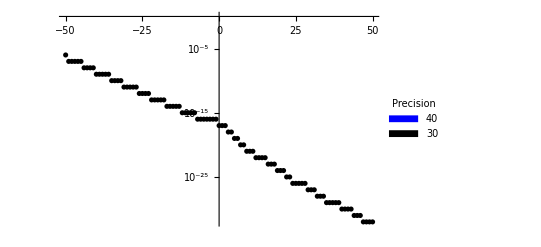

```mathematica
(*
  Create a plot of the differnces between the sum of the integer powers of the branch expansions to that of the corresponding summatory power coefficient
  *)
summatoryDifTable=Table[
branchCoefficientSum=Plus@@( MapThread[Coefficient[Plus@@#1[[2,All,4]] ,z,expVal] #2&,{alphaSeriesSet,Length@#&/@alphaMonodromyList}]);
summatoryCoef= Coefficient[pSumF[z],z,expVal];
termSize=MantissaExponent[Abs@summatoryCoef][[2]];
coefDif=MantissaExponent[Abs[branchCoefficientSum-summatoryCoef]][[2]];
{expVal,branchCoefficientSum,summatoryCoef,coefDif,termSize},
{expVal,Range[Sequence@@summatoryExpRange]}
];
(*summatoryDifTable[[{17,18}]]*)
(*accuracyPlot30=ListPlot[summatoryDifTable[[All,{1,4}]],PlotStyle->Black];*)
accuracyPlot30=ListPlot[summatoryDifTable[[All,{1,4}]],PlotStyle->Black,PlotLegends->Placed[SwatchLegend[{Blue,Black},{"40","30"},LegendLabel->Style["Precision",Bold,Black]],{0.8,0.5}],Ticks->{Automatic,{{-5,Superscript[10,-5]},{-10,Superscript[10,-10]},{-15,Superscript[10,-15]},{-20,Superscript[10,-20]},{-25,Superscript[10,-25]},{-30,Superscript[10,-30]},{-35,Superscript[10,-35]},{-40,Superscript[10,-40]}}},TicksStyle->Directive[Black,Bold,12]]
```

### Section 9.10.5: Other summatory funtion plot and summatorySeries plots

```mathematica
(*
 Generate summatory plot from sum of the integer powers of branch series
*)
summatoryBranchSumSeriesPlot=ParametricPlot3D[{Re@(z+translateFactor),Im@(z+translateFactor),Re@summatoryBranchSumSeriesF[z]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Darker@Green}]
summatoryPlotRange=PlotRange[summatorySeriesPlot];
```

-Graphics3D-

```mathematica
Show[{sumFPlot,summatoryLaurentSeriesPlot,summatoryBranchSumSeriesPlot}]
```

-Graphics3D-

```mathematica
(*
 Generate summatory plot
*)

summatorySeriesPlot=ParametricPlot3D[{Re@z,Im@z,Re@sumF[z+translateFactor]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(S_f(z))",12,Bold,Black]},PlotStyle->{Opacity[0.55],Red}]
summatoryPlotRange=PlotRange[summatoryPlot];
```

-Graphics3D-

PlotRange::gtype: Symbol is not a type of graphics.

```mathematica
(*
 Generate summatory series plot
*)
summatorySeriesPlot=ParametricPlot3D[{Re@z,Im@z,Re@sPSeries[z]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Blue}]
summatoryPlotRange=PlotRange[summatoryPlot];
```

-Graphics3D-

```mathematica
(*
 Generate summatory plot using sum of branch series
*)
sPSeriesPlot=ParametricPlot3D[{Re@z,Im@z,Re@summatorySeriesF[z]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Green}]
summatoryPlotRange=PlotRange[summatoryPlot];
```

-Graphics3D-

```mathematica
GraphicsRow[{summatoryPlot,summatorySeriesPlot,sPSeriesPlot}]
```

-Graphics-

## Section 7.5: Summary property 9.4.4 : The summary residue r_s is equal to the sum of the enclosed polar residues. Summary property 9.4.5: Sum of polar residues is equal to cyclic sum of branch residues

### Section 7.5.1: Check of summary property 9.4.4:

```mathematica
Print[Style[Grid[Prepend[poleResidueTableReport,{"Pole index","Residues","Sum","Running sum"}],Alignment->Center,Dividers->{{{True}},{True,True,{False},True}}],8]]
```

Pole index | Residues | Sum | Running sum |  | 
7 | {-0.00233483-0.902257 ⅈ} | -0.00233483-0.902257 ⅈ | -0.00233483-0.902257 ⅈ | 0.94082 | (-0.202335-1.14962 ⅈ)+0.94082 2.71828^((0.+1. ⅈ) t)
8 | {-0.00233483+0.902257 ⅈ} | -0.00233483+0.902257 ⅈ | -0.00466967+0. ⅈ | 0.94082 | (-0.202335+1.14962 ⅈ)+0.94082 2.71828^((0.+1. ⅈ) t)
33 | {1.45188-1.11329 ⅈ} | 1.45188-1.11329 ⅈ | 1.44721-1.11329 ⅈ | 0.94082 | (1.05188-1.1266 ⅈ)+0.94082 2.71828^((0.+1. ⅈ) t)
34 | {1.45188+1.11329 ⅈ} | 1.45188+1.11329 ⅈ | 2.89908+0. ⅈ | 0.94082 | (1.05188+1.1266 ⅈ)+0.94082 2.71828^((0.+1. ⅈ) t)
37 | {-0.899084} | -0.899084 | 2.+0. ⅈ | 1.41548 | -1.69909+1.41548 2.71828^((0.+1. ⅈ) t)

```mathematica
Print["nSumResidue computed in Section 7.4: ",nSumResidue//N]
```

nSumResidue computed in Section 7.4: 1.44954+2.01555 ⅈ

```mathematica
enclosedResidueSum=Plus@@poleResidueTable[[{2,4},3]];
Print["sum of enclosed pole residues: ",enclosedResidueSum//N]
```

sum of enclosed pole residues: 1.44954+2.01555 ⅈ

```mathematica
(*
 get branch expansions in non-central domain
*)

Precision@alphaSeriesSet[[All,2,All,4]]
branchCoefficientSum=Plus@@( MapThread[Coefficient[Plus@@#1[[2,All,4]],z,-1] #2&,{alphaSeriesSet,Length@#&/@alphaMonodromyList}]);
Print["Cyclic sum of branch residues: ",branchCoefficientSum//N];
Print["Cyclic sum of enclosed pole residues: ",enclosedResidueSum//N];
Print["nSumF residue: ",nSumResidue//N];
```

30.

Cyclic sum of branch residues: 1.44954+2.01555 ⅈ

Cyclic sum of enclosed pole residues: 1.44954+2.01555 ⅈ

nSumF residue: 1.44954+2.01555 ⅈ

```mathematica
latexErrorString=colorAccuracyReport4[enclosedResidueSum,branchCoefficientSum,pSumFResidue,Re,50,"Pole Sum: ","Branch sum: ","pSumF residue"]
```

Pole Sum:  | 1.449541916599986435076401787790602419187267505862
Branch sum:  | 1.449541916599986425453691225907315603700983536330
pSumF residue | 1.449541916599986435076401793058429531744226080090

Total accurate digits: 16

type is im

Pole Sum:  | 2.015549846988696343334376998798712947744257723612i
Branch sum:  | 2.015549846988696354494829992369383033543025957152i
pSumF residue | 2.015549846988696343334376994760936782522901215199i

Total accurate digits: 16

{\begin{array}{cl}\text{Actual val:}&\texttt{2.015549846988696343334376998798712947744257723612i}\\\text{Integral val:}&\texttt{2.0155498469886963}\color{red}\texttt{54494829992369383033543025957152i}\\\end{array},\text{second val: }&\texttt{2.01554984698869634333437699}\color{red}\texttt{4760936782522901215199}

## Section 7.6: Summatory property 9.4.6: Analytic domain of summatory is determined by distances to nearest singular points using alpha domain

### Section 7.6.1: Set up parameters for alpha-domain

```mathematica
translateFactor=1/2+3/2 I;

innerR=Abs[translateFactor-$theSingularList[[20]]];
outerR=Abs[translateFactor-$theSingularList[[42]]];
innerR//N
outerR//N

medialR=innerR+(outerR-innerR)/2;

alphaContourF[t_]:=translateFactor+medialR Exp[I t];

NearestTo[20,3][{1,2,4,8,16,32}]

nearestList=NearestTo[translateFactor,Length@$theSingularList][$theSingularList];

Position[nearestList,x_/;Abs[x-$theSingularList[[5]]]<10^-20]
$poleIndexes
$theSingularList[[$poleIndexes]]//N
innerLimit=Abs[translateFactor-$theSingularList[[8]]]//N
outerLimit=Abs[translateFactor-$theSingularList[[37]]]//N
```

1.6039

2.05971

### Section 7.6.2: Draw non-central annular region with variable red contour

```mathematica
innerCircleG=Graphics@Circle[ReIm@translateFactor,innerR];
outerCircleG=Graphics@Circle[ReIm@translateFactor,outerR];

annularDomainG=Graphics@{Opacity[0.1],Blue,Annulus[ReIm@translateFactor,{1.62,2.07}]};

translateFactorG=Graphics@{PointSize[0.01],Darker@Green,Point@ReIm@translateFactor};

lowerCircleG=Graphics@{Dashed,Darker@Green,Circle[ReIm@translateFactor,0.785]};
upperCircleG=Graphics@{Dashed,Red,Circle[ReIm@translateFactor,2.66]};

zTest=alphaContourF[Pi/4];
testPointG=Graphics@{PointSize[0.01],Point@{ReIm@zTest}};


 Manipulate[

ppA=ParametricPlot[ReIm[translateFactor+theR Exp[I t]],{t,-Pi,Pi},PlotStyle->{Red}];
Show[{annularDomainG,singG,poleG,ppA,translateFactorG,innerCircleG,outerCircleG,testPointG,lowerCircleG,upperCircleG},Axes->True,AspectRatio->1,PlotRange->4.25,ImageSize->500],
{{theR,1/2},1/2,5}
]
```

Show::gcomb: Could not combine the graphics objects in Show[{annularDomainG,,,,translateFactorG,innerCircleG,outerCircleG,testPointG,lowerCircleG,upperCircleG},Axes→True,AspectRatio→1,PlotRange→4.25,ImageSize→500].

### Section 7.6.3: Re-create summatory function for testCase0001 and plot in alpha domain

```mathematica
(*
 create summatory function
*)
Options[nSumF]={"sumWP"->MachinePrecision};
nSumF[z_?NumericQ,OptionsPattern[]]:=Plus@@(w/.NSolve[$implicitF[z,w]==0,w,WorkingPrecision->OptionValue["sumWP"]]);

nSumFPlot= ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->translateFactor+r Exp[I t],{r,innerR,outerR},{t,0,2 Pi},BoxRatios->{1, 1, 1}];
nPlotRange=PlotRange@nSumFPlot;

plotN= Show[nSumFPlot,BoxRatios->{1, 1, 1},PlotStyle->LightBlue,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["N",12,Bold,Black]},FaceGrids->{{{0,0,-1},{Array[#&,{5},nPlotRange[[1]]],Array[#&,{5},nPlotRange[[2]]]}}},FaceGridsStyle->Directive[Black,Dashed],ViewPoint->{0,-5,2},ImageSize->300]
```

-Graphics3D-

### Section 7.6.4: Re-compute power expansion of summatory function in alpha domain

```mathematica
(*
 nSumF[z] power expansion user menu
*)
summatoryFunctionUserMenu=Labeled[Column[{Row[{Style["Partition size:",Black,Bold],Spacer[5],InputField[Dynamic@$partitionSize933b,FieldSize->2],Spacer[10],Style["Range:",Black,Bold],Spacer[5],InputField[Dynamic@$range933b,FieldSize->8]}],
Row[{Style["Precision:",Black,Bold],Spacer[5],InputField[Dynamic@$precision933b,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Summatory function power expansion user menu",Bold,Black],Top]
```

Partition size:Range:
Precision:Summatory function power expansion user menu

```mathematica
(*
 create nSumF[z] power expansions
*)
summatoryRange=Range[Sequence@@$range933b];

alphaSummatoryTerms=ParallelTable[
If[Mod[theK,25]==0,
Print["theK: ",theK];
];
If[theK==0,
theInt= NIntegrate[nSumF[alphaContourF[t],"sumWP"->$precision933b](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},
WorkingPrecision->$precision933b,AccuracyGoal->$precision933b/2,
Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},MaxRecursion->Infinity];
,
theInt= NIntegrate[nSumF[alphaContourF[t],"sumWP"->$precision933b](Cos[t theK]-I Sin[t theK]),{t,-Pi,Pi},
WorkingPrecision->$precision933b,AccuracyGoal->$precision933b/2,Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},MaxRecursion->Infinity]
];
coef=1/(2 Pi medialR^(theK))theInt;
{theK,coef,coef z^theK},
{theK,summatoryRange}
];
(*
 extract nSumf power expansion residue
*)
nSumResidue=Coefficient[Plus@@alphaSummatoryTerms[[All,3]],z,-1];
Print["Residue of summatory function: ",nSumResidue];
```

theK: -100

theK: -50

theK: -75

theK: -25

theK: 0

theK: 25

theK: 50

theK: 75

theK: 100

Residue of summatory function: 1.449541916599986435076401787790602419187267505799+2.0155498469886963433343769987987129477442577236154 ⅈ

### Section 7.6.5: Compute upper limit of convergence of summatory series using root test of analytic terms

(1.38543-0.337288 ⅈ)+(0.227822-0.445191 ⅈ) z+(0.132473+0.10465 ⅈ) z^2-(0.0299757-0.0311271 ⅈ) z^3-(0.00799026+0.0030534 ⅈ) z^4

test2

min residue: 3.079968

2.65912+2.33784 x-116.842 x^2+1470.78 x^3

Estimated upper annular convergence limit: 2.65912

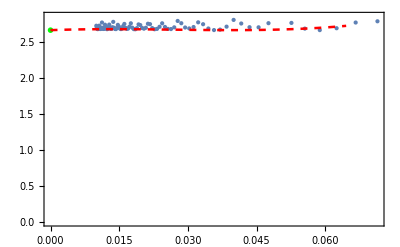

```mathematica
$rootTestLabel=False;


 analyticSeries= Plus@@alphaSummatoryTerms[[101;;,3]];
analyticSeries[[1;;5]]//N
cycleSize=1;

seriesLength=Length@analyticSeries;
theexp=Exponent[analyticSeries,z,List];
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[analyticSeries,z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleSize/numVals[[k]])),15]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,14,Black,Bold]];


 startTermIndex=5;
endTermIndex=-1;
dataVals=cTable[[startTermIndex;;endTermIndex]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;
Print["test2"];
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->15][[2]];
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2},WorkingPrecision->15][[2]];
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3},WorkingPrecision->15][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["min residue: ",residueSet[[bestFitPos]]];

Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];
fitResults=rTest;
Print["Estimated upper annular convergence limit: ",fitResults//N];
annularUpperR=fitResults;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.0075]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,14,Black,Bold]];

thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
Show[{lp1,plotSet[[bestFitPos]],fitValueG},PlotLabel->If[$rootTestLabel,Style["Analytic terms",Bold,Black]],ImageSize->400]
```

### Section 7.6.6: Compute lower limit of summatory function power expansion using singular terms

```mathematica
$singularRootTestLabel=False;
singularSeries= Plus@@alphaSummatoryTerms[[1;;100,3]];singularTerms=alphaSummatoryTerms[[1;;100,3]];
singularSeries[[1;;5]]//N
cycleSize=1;

seriesLength=Length@singularSeries;
theexp=Exponent[singularSeries,z,List];
theexp=Exponent[#,z]&/@ singularTerms;
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=MapThread[Coefficient[#1,z,#2]&,{singularTerms,theexp}];


cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleSize/numVals[[k]])),25]},
{k,5,Length@clist}];

(*Print["cTable Len: ",Length@cTable];*)
singularLp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},Frame->{{False,True},{True,False}},FrameTicks->{{None,All},Automatic},FrameLabel->{{None,Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},{Style["1/m_k",16,Bold,Black],None}},AspectRatio->1,FrameTicksStyle->Directive[Black,14,Black,Bold]];

singPlotRange=PlotRange[singularLp1];

dataValStart=10;
dataValEnd=-1;
dataVals=cTable[[dataValStart;;dataValEnd]];
plotXStart=0;
plotXEnd=dataVals[[10,1]];


linearLine=c0+c1 x/. Minimize[{Total[((c0+c1 #[[1]])-#[[2]])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated convergence domain: ",convergenceValue];
annularLowerR=convergenceValue;

convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};

theSingularPlotLabel=Style["Root Test of singular terms"];
singularBestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red},TicksStyle->Directive[Black,Bold,14]];
singularRootTestPlot=Show[{singularLp1,singularBestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},PlotRange->{{plotXStart,plotXEnd},Automatic},PlotLabel->If[$singularRootTestLabel,theSingularPlotLabel],ImageSize->400]
```

(3.35683×10^-11+8.99679×10^-12 ⅈ)/z^100-(4.33875×10^-11-8.8353×10^-12 ⅈ)/z^99+(4.444×10^-11-3.47501×10^-11 ⅈ)/z^98-(3.09005×10^-11-6.48936×10^-11 ⅈ)/z^97-(1.68005×10^-12+9.15589×10^-11 ⅈ)/z^96

residueSet: {68.5596,68.5596,0.0834131}

Best fit function: 0.7851-0.0930659 x-0.223871 x^2-26.4739 x^3

Minimum Residue: 0.0834131

Estimated convergence domain: 0.7851

-Graphics-

## Section 8: Generate summatory plots in extended domain based on root test

```mathematica
(*
 Generate summatory series plot
*)
alphaSummatoryF[z_]=Plus@@alphaSummatoryTerms[[All,3]];extendedSumPlot=ParametricPlot3D[{Re@(z+translateFactor),Im@(z+translateFactor),Re@alphaSummatoryF[z]}/.z->r Exp[I t],{r,annularLowerR,annularUpperR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(sF(z))",12,Bold,Black]},PlotStyle->{Opacity[0.5],Blue},PlotPoints->100];
summatoryPlotRange=PlotRange[extendedSumPlot];
 Show[{extendedSumPlot},ImageSize->300]
```

-Graphics3D-

```mathematica
(*
 generate nSumF plot in extended domain
*)
 nSumPlot= ParametricPlot3D[{Re@z,Im@z,Re@nSumF[z]}/.z->translateFactor+r Exp[I t],{r,annularLowerR,annularUpperR},{t,0,2 Pi},BoxRatios->{1, 1, 1},PlotPoints->100]
```

-Graphics3D-

## Initialization

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]
 $HistoryLength=0;
<<ComputationalGeometry`
$range933a={-100,100};
$partitionSize933a=1;
$precision933a=30;


$precision933b=30;
 $property932Annulus=1;
$property932Precision=30;
 $selectedAnnulus922=1;
$precision922=30;

 $property931Annulus=1;

$range933a={-100,100};
$partitionSize933a=1;
$precision933a=30;


(*
 end of new terms
*)


 $property921Precision=30;
$property921Annulus=1;




 $accuracyComparisonFactor=20;
$radialSegments=13;
$arcSegments=48;

$selectedAnnulus=1;
$selectedMonodromyIndex=1;
$plotType=Re;
$showPlotLabel=False;

$tempAnnulusIndex=1;
$tempMonodromyIndex=1;
$coefficientPower=1;
$firstAnnulus=1;
$secondAnnulus=2;
$phiPrecision=15;
$partitionSize=1;
$partitionSize933=1;

$selectedAnnulus933=1;
 $doPolishFlag933=False;
$polishPrecision933=30;
$precision933=30;

 $doPolishFlag931=False;
$polishPrecision931=30;

 $doPolishFlag932=False;
$polishPrecision932=30
$selectedAnnulus932=1;

 $selectedAnnulus933b=1;
$partitionSize933b=1;
$doPolishPrecision933b=False;
$polishPrecision933b=30
$exponent933b=1;
$range933b={-5,5};

 $selectedAnnulus934=1;
$partitionSize934=1;
$range934={-2,2};
$exponent934=-1;
$polishPrecision934=30;
$doPolishFlag934=False;

 $selectedAnnulus9111=1;
$partitionSize9111=1;
$range9111={-5,5};
$exponent9111=-1;
$doPolishFlag9111=False;
$polishPrecision9111=30;
$doPolishFlag933c=False;
$range933d={-10,10};
$partitionSize933d=1;
$polishPrecision933d=30;
$doPolishFlag933d=False;

 $doPolishFlag933e=False;
$partitionSize933e=1;
$range933e={-100,100};
$polishPrecision933e=30;
$selectedPrecision=30;


DistributeDefinitions[ConvexHull];
 $userDirectory="D:\\puiseuxSeries";
 $fNewton=Table[0,100];
 $λNewton=Table[0,100];
 $βNewton=Table[0,100];
 $cNewton=Table[0,100];
 $puiseuxSave={};
(* $separationFactor=10;*)
 $workingPrecision=1000;
 $acf=20;
 $rcf=50;
 $charRootFactor=100;



 $useReformedFunctionFlag=True;
 $printCResidueKeyFlag=False;
 $maxPolymodalIteration=15;
 $showSegmentFlag=False;
 $stiffnessSwitchingFlag=True;
 $integrationDiagFlag1=False;
 $integrationDiagFlag2=False;
 $removeCSubResidueFactor=50;
 $mcf=50;
 $maxRootVerifyDifference=10^-50;
 $savePolygonFigures=False;
 $polygonFigures={};

 $saveRootTallyListFlag=False;
 $saveNewtonIterationDataFlag=False;
 $tallyNewtonIterationIndexFlag=False;
 $getIterationNumbersFlag=False;
 $minimalWorkingAccuracy=100;
 $thetaV=Pi/6;
 $saveFIterateFlag=False;
 $pzf=100;
 $printPolishRootFlag=False;




 $getSegmentDataFlag=False;
 $getCharRootFlag=False;
 $getPoleDataFlag=False;
 $getNewtonDataFlag=False;
 $minCharRootAccuracy=100;

DistributeDefinitions[ z,
 w,
 c,
 s,
 $workingPrecision
];

 file::fileExists="File `1` exists.";


(*$convertToNormalFormResidueFactor=10^(-50);*)
(*$removableNewtonDataResidueFactor=10^(-50);*)
(*$integrationDataResidueFactor=10^(-50);*)
$showNormalizedConstants=False;
$minNSolvePrecision=100;

colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];
theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];

Quiet[Select[Names["System`*"],Attributes[#]==={Protected}&&ColorQ[ToExpression[#]]&]]
{"Black","Blue","Brown","Cyan","Gray","Green","LightBlue","LightBrown","LightCyan","LightGray","LightGreen","LightMagenta","LightOrange","LightPink","LightPurple","LightRed","LightYellow","Magenta","Orange","Pink","Purple","Red","Transparent","White","Yellow"}
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
colorTable=Flatten@theColorList;
colorTable[[1;;10]]={Blue,Red,Yellow,Brown,Cyan,Green,Orange,Pink,Purple,Magenta}
```

30

30

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0.6, 0.4, 0.2],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 1]}

### getSingularPoints (new)

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
  getSingularPoints[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,rNormArray
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];
minRadiusArray=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];
For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray={2};
nearestDistArray={4};
rNormArray={2}
];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### getSingularPointsOld

```mathematica
getSingularPointsOld[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];

at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
minRadiusArray=nearestDist;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### polyForm(poly,var)

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### getMinValidExp

```mathematica
getMinValidExp[singIndex_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+$theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidExpForGenus[singIndex_,theSingularList_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];


getMinValidExpInf[]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidTransFunction[f_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[f];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$acf;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getRootTestResults

```mathematica
(*
 function for Root Test
*)
getRootTestResults[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_,$theTestCase_]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable,m,k},

cycleBaseSheets=baseSheetLinks[[All,2,1]];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=graphicsData[[All,5]];

rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];

rootTestReport=Prepend[rootTestReport1,{"Index","Sheet","Type","Size","Root Test","Series size"}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)
rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];

rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];

rootTestReportHeader=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];

{rootTestResults2,finalReport,rootTestReportHeader,graphicsData}

(*{rootTestReport1,rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}*)

]; (* end of module *)
```

### getBranchIDs

```mathematica
(*
 identify branc sheets 
*)
getBranchIDs[baseSeries_,baseSheetLinks_,baseRemovableList_]:=Module[{seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,typeTable,minE,theD,type,theN,theTally,mVals,j,i,typeLoc ,baseSheetNumbers,sheetNumbers},

 baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
(*Print["baseSheetNumbers: ",baseSheetNumbers];*)

seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];

multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];

 (* 
pick out Taylor series:
*)
typeTable=Table[
sheetNumbers=baseSheetLinks[[i,2]];
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[Flatten[baseRemovableList[[baseSheetLinks[[i,2]]]][[All,2]]]!={},
(*If[baseRemovableList[[i,2]]!={},*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",theD,theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",theD,theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",theD,theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
];
(*
typeTable,minE,baseRemovableList,theD,type,theN,theTally,mVals,j,i,typeLoc 
*)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];

MapThread[{#1,#2}&,{typeTable,baseSheetLinks[[All,2]]}]
];
```

### plotBranchSeries

```mathematica
plotBranchSeries[baseSingularPoint_,theBranchSeries_,sheetLinks_,estR_,colors_,type_]:=
Module[{genF,theExp,theNum,cList,f,thePlots,cycleSize,domain},
cycleSize=Length@sheetLinks;
genF[u_]=theBranchSeries[[sheetLinks[[1]],1;;50]];
theExp=Exponent[genF[z],z,List];
theNum=Numerator@theExp;
cList=Coefficient[genF[z],z,theExp];
f[z_,k_]:=Sum[cList[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theExp[[n]]) z^theExp[[n]],{n,1,Length[cList]}];
domain={1/50,estR};
Table[
 ParametricPlot3D[{Re[z]+Re[baseSingularPoint],Im[z]+Im[baseSingularPoint],type[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,domain[[1]],domain[[2]]},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.55],colors[[i]]}],
{i,1,cycleSize}]

(*Show[thePlots,BoxRatios->{1,1,1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGridsStyle->Directive[Black,Bold],AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style[ToString@type<>"(w)",12,Bold,Black]},PlotRange->All,ImageSize->300]*)
]
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\singularData.m"}] ;
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTable.m"}];

annularMonodromyTableGraphicsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromyTableGraphics.jpg" }];
singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularMonodromies.m"}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
 
summatorySeriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`summatorySeries.m"][testCase,ToString@k]}];
annularTableWithBranchLinksFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithBranchLinks.m"}];
combinedExpansionTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`combinedExpansionTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularTableWithMonodromies.m" }];
```

### getAnnularTemplate

```mathematica
getAnnularTemplate[theFunction_]:=Module[{res,theSingularSet,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,absVals,ringSize,tempRings,theAnnuli,ringMemberSingularIndexes,radiiTable,annularSizes,annularCenters,singTable,annulusTable,annulusTableR,ringSizes,minRingSize,tableIndex,j,annulusTableReport,singTableAnnulusIndexes,plottingRadiiTable,newTable,theReturn,singTableSingIndexes,i },




(*totalIntegrationSteps=1500000;*)
(*maxStepSize=0.0001;*)

(*ringDelta=1/20000;*) (* ring separation threshold *)
minRingSize=1/2000;



res=Resultant[theFunction,D[theFunction,w],w];

theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];


singAccuracy=Floor@Accuracy@theSingularSet;

(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points argList,zeroIndexes,poleIndexes,nearestSing,nearestDist
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[theFunction,theSingularList,False];
Print["poleIndexes: ",poleIndexes];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];


minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];

(*
  compute annular regions 
*)

tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+4}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,$radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[($radialSegments-1)/2+1]],0]&/@ radiiTable;

(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)

(*  *)



singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

Print["Routine for singular point at zero"];


(* first add 0  *)
If[poleIndexes!={},
If[poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];

(* do annulusTable here *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
]
,
singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];

,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
];
(* gives index into annulusTable for an annulus *) singTableAnnulusIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
singTableSingIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

plottingRadiiTable=Table[
newTable=radiiTable[[tableIndex]];
newTable[[1]]=newTable[[1]]+(newTable[[2]]-newTable[[1]])/10;
newTable[[-1]]=newTable[[-1]]+(newTable[[-2]]-newTable[[-1]])/10;
newTable,
{tableIndex,1,Length@radiiTable}];

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}

];
```

### getSingularData

```mathematica
getSingularData[testCase_,baseSingularIndex_]:=Module[{baseSingularPoint,baseRadius,dataList,baseBranchTypeArray,baseSeriesMIVPTable,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,return},

 If[TrueQ@FileExistsQ@seriesFileName[testCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
(*Print["baseSingularPoint: ",$theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[baseSingularIndex]];*)
dataList=Import[seriesFileName[testCase,baseSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList!=11,
Print[Style["This notebook requires Vers.3.0 Puiseux series data with baseSeriesMIVPTable",Red]];
Abort[];
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
(*Print[baseSeries[[All,1;;4]]//N//MatrixForm];*)
return={newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable};
,
Print[Style["Singular file "<>seriesFileName[testCase,baseSingularIndex]<>" not found",Red]];
return=Table[False,{11}];
];
return
];
```

### getAnnularMonodromy

```mathematica
(*
 get differential monodromy around a selected annulus
*)
Options[getAnnularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"stiffFlag"->False,"diagFlag"->False};
getAnnularMonodromy[annulusIndex_,annularNorms_,OptionsPattern[]]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable},

rNorm=annularNorms[[annulusIndex]];
z0=rNorm Exp[I $thetaV];
If[OptionValue["diagFlag"],
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[OptionValue["diagFlag"],
Print[Grid[SetPrecision[wArray,4]]];
];

 branchVals=integrateOverAnnulus[$thetaV,wArray,rNorm,OptionValue["integrateWP"],OptionValue["stiffFlag"]];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[OptionValue["diagFlag"],
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[OptionValue["diagFlag"],
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["monodromy is inconsistent!",Red]];
,
Print["monodromy is consistent"];
];
{z0,rNorm,finalCycles,polishedVals}
];
```

### getSingTableIndexes

```mathematica
getSingTableIndexes[singTable_,annulus_]:=Module[{singMembers,singIndexes,annulusIndex,return},
If[annulus>Length@theAnnuli || annulus<0,
Print[Style["Annulus number out of range!",Red]];
return=-1;
,
annulusIndex=singTableAnnulusIndexes[[annulus]];
If[annulus==Length@theAnnuli,
singIndexes={-1};
,
singMembers=ringMemberSingularIndexes[[annulus]];
singIndexes=singTableSingIndexes[[singMembers]];
];
return={annulusIndex,singIndexes};
];
return
]
```

### getMedialStartVals

```mathematica
getMedialStartVals[annulusTable_,$selectedAnnulus_,$selectedMonodromyIndex_,$thetaV_,implicitF_]:=Module[{aIndex,sIndex,$selectedMonodromyList,$selectedBranchSize,rNorm,zStart,theRoots,wStart},
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,$selectedAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
$selectedBranchSize=Length@$selectedMonodromyList[[$selectedMonodromyIndex]];

rNorm=annulusTable[[aIndex,4]];
(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)
zStart=rNorm Exp[I $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];

wStart=theRoots[[$selectedMonodromyList[[$selectedMonodromyIndex,1]]]];
{rNorm,zStart,wStart}
];
```

### getAnnularIntegrations

```mathematica
Options[getAnnularIntegrations]={"ndSolveWP"->MachinePrecision,"intWP"->MachinePrecision,"polish"->False,"polishPrec"->50,"accGoal"->6};

getAnnularIntegrations[annulusTable_,testAnnulus_,OptionsPattern[]]:=Module[{aIndex,sIndexes,selectedMonodromies,theMonodromy,theBranchSize,rNorm,zStart,wStart,tStart,tEnd,integrationPath,wDeriv,theSol},
{aIndex,sIndexes}=getSingTableIndexes[annulusTable,testAnnulus];
selectedMonodromies=annulusTable[[aIndex,6]];
Print["selectedMonodromies: ",selectedMonodromies];

Table[
Print["Analyzing branch: ",selectedMonodromies[[monodromyIndex]]];
theMonodromy=selectedMonodromies[[monodromyIndex]];
theBranchSize=Length@theMonodromy;
{rNorm,zStart,wStart}=getMedialStartVals[annulusTable,testAnnulus,monodromyIndex,$thetaV,$implicitF];
tStart=$thetaV;
tEnd=$thetaV+2 Pi theBranchSize;

integrationPath[t_]:=rNorm Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->OptionValue["ndSolveWP"]];
Print["Precision of NDSolve solution: ",Precision@theSol];
If[OptionValue["polish"],
NIntegrate[ polishMedial[t,rNorm,$implicitF,theSol[t],OptionValue["polishPrec"]]D[integrationPath[t],t],{t,tStart,tEnd},WorkingPrecision->OptionValue["polishPrec"],MaxRecursion->Infinity,AccuracyGoal->OptionValue["accGoal"]]
(*NIntegrate[ polishMedial[t,rNorm,$implicitF,theSol[t],OptionValue["polishPrec"]]D[integrationPath[t],t],{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->OptionValue["polishPrec"],MaxRecursion->Infinity,AccuracyGoal->30]*)
,
NIntegrate[theSol[t] D[integrationPath[t],t],{t,tStart,tEnd},WorkingPrecision->OptionValue["intWP"],MaxRecursion->Infinity,AccuracyGoal->OptionValue["accGoal"]]
(*NIntegrate[theSol[t] D[integrationPath[t],t],{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->OptionValue["intWP"],MaxRecursion->Infinity,AccuracyGoal->6]*)
],
{monodromyIndex,1,Length@selectedMonodromies}
]
];
```

### polishMedial

```mathematica
(*polishMedial[t,rNorm,$implicitF,theSol[t],50]*)

 polishMedial[t_?NumericQ,r_?NumericQ,implicitF_,medialVal_?NumericQ,wPrec_?NumericQ]:=Module[{},
w/.FindRoot[implicitF[r Exp[I t],w]==0,{w,medialVal},WorkingPrecision->wPrec,AccuracyGoal->wPrec,PrecisionGoal->wPrec]
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["polishTerms error below $maxErrorTolerance: ",Red,Bold,14]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,wp_,stiffnessFlag_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)

{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
(*Print["intTable: ",intTable//N];*)
intTable
];
```

### getSeriesTypes

```mathematica
baseRemovableList
```

baseRemovableList

```mathematica
getSeriesTypes[baseSeries_,baseSheetLinks_,baseRemovalList_]:=Module[{baseSheetNumbers,seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,minE,type,theD,theN, theTally,mVals,j,typeLoc,i,typeTable },
(*
 uniquely name each branch
*)

baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];
multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];
 (* 
pick out Taylor series: 
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[baseRemovableList[[i,2]]!={},
(*If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
]; (* theTally,mVals,j,typeLoc,i,typeTable *)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
{typeTable,baseSheetNumbers,seriesLengths}

];
```

### getSummatoryRootTest

```mathematica
getSummatoryRootTest[summatorySeries_,poleIndex_]:=Module[{seriesLength,cycleType,theexp,lcm,numVals,cList,cTable,lp1,startTerms,dataVals,plotXStart,plotXEnd,endTerms,seriesType,graphicsData,linearLine,quadraticLine,cubicLine,linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,plotFlag,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,clist},

seriesLength=Length@summatorySeries;
cycleType=1;
theexp=Exponent[summatorySeries,z,List];
lcm=LCM@@(Denominator@theexp);
        numVals=lcm theexp;
clist=Coefficient[summatorySeries,z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];

(**)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.0105]},AxesOrigin->{0,0},PlotRange->All];


startTerms=10;
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;
seriesType="L_-1";
graphicsData={};
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

(* *)
linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;
Print["Extrapolated value: ",fitResults//N];

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};
plotFlag=False;

(*plotSet,plotFlag,fitValueG,plotLabel,thePlotRange,xCoord*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[poleIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
graphicsData
];
```

### convertToChar

```mathematica
convertToChar[num_]:=Module[{sTest,s1,newS,newS2},
sTest=ToString@AccountingForm@num;
s1=StringTake[sTest,1];
If[s1=="(",
newS=StringReplacePart[sTest,"-",{1,1}];
newS2=StringDrop[newS,-1];
Characters@newS2
,
Characters@sTest
]
];
```

### colorAccuracyReport

```mathematica
colorAccuracyReport4[actualValue_,approxValue1_,approxValue2_,type_,maxChar_,string1_,string2_,string3_]:=Module[{realBaseVal,actWChar,actWCharRow,realSeriesVal1,seriesWChar1,seriesWCharRow1,maxCharFlag,i,dotValue,errorData,actString,serString,latexCode,seriesCharSave1,seriesCharSave2,seriesWChar2,realSeriesVal2,seriesWCharRow2,i2,latexCode2,serString2,theType},
(*
 do real part here
*)
theType=Re;
realBaseVal=theType@actualValue;
actWChar=convertToChar[SetPrecision[realBaseVal,maxChar]];
actWCharRow={Style["Actual Value",8],Style[Row[actWChar[[1;;maxChar]]],8]};

realSeriesVal1=theType@approxValue1;
seriesWChar1=convertToChar[SetPrecision[realSeriesVal1,maxChar]];
seriesWCharRow1={Style["Integral val",8],Style[Row[seriesWChar1[[1;;maxChar]]],8]};

realSeriesVal2=theType@approxValue2;
seriesWChar2=convertToChar[SetPrecision[realSeriesVal2,maxChar]];
seriesWCharRow2={Style["Integral val",8],Style[Row[seriesWChar2[[1;;maxChar]]],8]};

maxCharFlag=False;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar1[[i]] && i<maxChar,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];
seriesCharSave1=seriesWChar1;
If[i==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

(* 
do second val
*)
i2=1;
dotValue=0;
While[actWChar[[i2]]==seriesWChar2[[i2]] && i<maxChar,
i2++;
If[actWChar[[i2]]==".",
dotValue=i2;
];
];
seriesCharSave2=seriesWChar2;
If[i2==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

If[maxCharFlag,
Print[Style["Max characters reached",Red]];
Abort[];
,
For[k=1,k<=i-1,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Black,Bold];
];
For[k=1,k<=i2-1,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Black,Bold];
];


For[k=i,k<=maxChar,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Red];
];
For[k=i2,k<=maxChar,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Red];
];


If[theType===Re,
actString=actWChar[[1;;maxChar]];
,
actString=Join[actWChar[[1;;maxChar]],{"i"}];
];

If[theType===Re,
serString=seriesWChar1[[1;;maxChar]];
,
serString=Join[seriesWChar1[[1;;maxChar]],{"i"}];
];

If[theType===Re,
serString2=seriesWChar2[[1;;maxChar]];
,
serString2=Join[seriesWChar2[[1;;maxChar]],{"i"}];
];

latexCode="\\begin{array}{cl}\\text{Actual val:}&\\texttt{"<>actString<>"}"<>"\\\\"<>"\\text{Integral val:}&";
latexCode=latexCode<>"\\texttt{"<>seriesCharSave1[[1;;i-1]]<>"}";

latexCode2="\\text{second val: }&\\texttt{"<>seriesCharSave2[[1;;i2-1]]<>"}";
latexCode2=latexCode2<>"\\color{red}"<>"\\texttt{"<>seriesCharSave2[[i2;;maxChar]];

latexCode=latexCode<>"\\color{red}"<>"\\texttt{"<>seriesCharSave1[[i;;maxChar]]<>If[type===Im,"i"<>"}\\\\\\end{array}"
,
"}\\\\\\end{array}"
];

errorData={{Style[string1,10],Style[Row[actString],10]},
{Style[string2,10],Style[Row[serString],10]},
{Style[string3,10],Style[Row[serString2],10]}};
Print[Grid[errorData]];
Print["Total accurate digits: ",i-1-dotValue];
];
(*
 do imag part
*)
theType=Im;
realBaseVal=theType@actualValue;
actWChar=convertToChar[SetPrecision[realBaseVal,maxChar]];
actWCharRow={Style["Actual Value",8],Style[Row[actWChar[[1;;maxChar]]],8]};

realSeriesVal1=theType@approxValue1;
seriesWChar1=convertToChar[SetPrecision[realSeriesVal1,maxChar]];
seriesWCharRow1={Style["Integral val",8],Style[Row[seriesWChar1[[1;;maxChar]]],8]};

realSeriesVal2=theType@approxValue2;
seriesWChar2=convertToChar[SetPrecision[realSeriesVal2,maxChar]];
seriesWCharRow2={Style["Integral val",8],Style[Row[seriesWChar2[[1;;maxChar]]],8]};

maxCharFlag=False;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar1[[i]] && i<maxChar,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];
seriesCharSave1=seriesWChar1;
If[i==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

(* 
do second val
*)
i2=1;
dotValue=0;
While[actWChar[[i2]]==seriesWChar2[[i2]] && i<maxChar,
i2++;
If[actWChar[[i2]]==".",
dotValue=i2;
];
];
seriesCharSave2=seriesWChar2;
If[i2==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

If[maxCharFlag,
Print[Style["Max characters reached",Red]];
Abort[];
,
For[k=1,k<=i-1,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Black,Bold];
];
For[k=1,k<=i2-1,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Black,Bold];
];


For[k=i,k<=maxChar,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Red];
];
For[k=i2,k<=maxChar,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Red];
];


If[theType===Re,
actString=actWChar[[1;;maxChar]];
,
Print["type is im"];

actString=Join[actWChar[[1;;maxChar]],{"i"}];
];

If[theType===Re,
serString=seriesWChar1[[1;;maxChar]];
,
serString=Join[seriesWChar1[[1;;maxChar]],{"i"}];
];

If[theType===Re,
serString2=seriesWChar2[[1;;maxChar]];
,
serString2=Join[seriesWChar2[[1;;maxChar]],{"i"}];
];

latexCode="\\begin{array}{cl}\\text{Actual val:}&\\texttt{"<>actString<>"}"<>"\\\\"<>"\\text{Integral val:}&";
latexCode=latexCode<>"\\texttt{"<>seriesCharSave1[[1;;i-1]]<>"}";

latexCode2="\\text{second val: }&\\texttt{"<>seriesCharSave2[[1;;i2-1]]<>"}";
latexCode2=latexCode2<>"\\color{red}"<>"\\texttt{"<>seriesCharSave2[[i2;;maxChar]];

latexCode=latexCode<>"\\color{red}"<>"\\texttt{"<>seriesCharSave1[[i;;maxChar]]<>If[theType===Im,"i"<>"}\\\\\\end{array}"
,
"}\\\\\\end{array}"
];


errorData={{Style[string1,10],Style[Row[actString],10]},
{Style[string2,10],Style[Row[serString],10]},
{Style[string3,10],Style[Row[serString2],10]}};
Print[Grid[errorData]];
Print["Total accurate digits: ",i-1-dotValue];
];
{latexCode,latexCode2}
];
```

```mathematica
colorAccuracyReport3[actualValue_,approxValue1_,approxValue2_,type_,maxChar_,string1_,string2_,string3_]:=Module[{realBaseVal,actWChar,actWCharRow,realSeriesVal1,seriesWChar1,seriesWCharRow1,maxCharFlag,i,dotValue,errorData,actString,serString,latexCode,seriesCharSave1,seriesCharSave2,seriesWChar2,realSeriesVal2,seriesWCharRow2,i2,latexCode2,serString2},
realBaseVal=type@actualValue;
actWChar=convertToChar[SetPrecision[realBaseVal,maxChar]];
actWCharRow={Style["Actual Value",8],Style[Row[actWChar[[1;;maxChar]]],8]};

realSeriesVal1=type@approxValue1;
seriesWChar1=convertToChar[SetPrecision[realSeriesVal1,maxChar]];
seriesWCharRow1={Style["Integral val",8],Style[Row[seriesWChar1[[1;;maxChar]]],8]};

realSeriesVal2=type@approxValue2;
seriesWChar2=convertToChar[SetPrecision[realSeriesVal2,maxChar]];
seriesWCharRow2={Style["Integral val",8],Style[Row[seriesWChar2[[1;;maxChar]]],8]};

maxCharFlag=False;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar1[[i]] && i<maxChar,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];
seriesCharSave1=seriesWChar1;
If[i==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

(* 
do second val
*)
i2=1;
dotValue=0;
While[actWChar[[i2]]==seriesWChar2[[i2]] && i<maxChar,
i2++;
If[actWChar[[i2]]==".",
dotValue=i2;
];
];
seriesCharSave2=seriesWChar2;
If[i2==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];

If[maxCharFlag,
Print[Style["Max characters reached",Red]];
Abort[];
,
For[k=1,k<=i-1,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Black,Bold];
];
For[k=1,k<=i2-1,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Black,Bold];
];


For[k=i,k<=maxChar,k++,
seriesWChar1[[k]]=Style[seriesWChar1[[k]],Red];
];
For[k=i2,k<=maxChar,k++,
seriesWChar2[[k]]=Style[seriesWChar2[[k]],Red];
];


If[type===Re,
actString=actWChar[[1;;maxChar]];
,
actString=Join[actWChar[[1;;maxChar]],{"i"}];
];

If[type===Re,
serString=seriesWChar1[[1;;maxChar]];
,
serString=Join[seriesWChar1[[1;;maxChar]],{"i"}];
];

If[type===Re,
serString2=seriesWChar2[[1;;maxChar]];
,
serString2=Join[seriesWChar2[[1;;maxChar]],{"i"}];
];

latexCode="\\begin{array}{cl}\\text{Actual val:}&\\texttt{"<>actString<>"}"<>"\\\\"<>"\\text{Integral val:}&";
latexCode=latexCode<>"\\texttt{"<>seriesCharSave1[[1;;i-1]]<>"}";

latexCode2="\\text{second val: }&\\texttt{"<>seriesCharSave2[[1;;i2-1]]<>"}";
latexCode2=latexCode2<>"\\color{red}"<>"\\texttt{"<>seriesCharSave2[[i2;;maxChar]];

latexCode=latexCode<>"\\color{red}"<>"\\texttt{"<>seriesCharSave1[[i;;maxChar]]<>If[type===Im,"i"<>"}\\\\\\end{array}"
,
"}\\\\\\end{array}"
];


errorData={{Style[string1,10],Style[Row[actString],10]},
{Style[string2,10],Style[Row[serString],10]},
{Style[string3,10],Style[Row[serString2],10]}};
Print[Grid[errorData]];
Print["Total accurate digits: ",i-1-dotValue];
];
{latexCode,latexCode2}
];
```

```mathematica
colorAccuracyReport2[actualValue_,approxValue_,type_,maxChar_,string1_,string2_]:=Module[{realBaseVal,actWChar,actWCharRow,realSeriesVal,seriesWChar,seriesWCharRow,maxCharFlag,i,dotValue,errorData,actString,serString,latexCode,seriesCharSave},
realBaseVal=type@actualValue;
actWChar=convertToChar[SetPrecision[realBaseVal,maxChar]];
actWCharRow={Style["Actual Value",8],Style[Row[actWChar[[1;;maxChar]]],8]};
realSeriesVal=type@approxValue;
seriesWChar=convertToChar[SetPrecision[realSeriesVal,maxChar]];
seriesWCharRow={Style["Integral val",8],Style[Row[seriesWChar[[1;;maxChar]]],8]};
maxCharFlag=False;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxChar,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];
seriesCharSave=seriesWChar;
If[i==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];
If[maxCharFlag,
Print[Style["Max characters reached",Red]];
Abort[];
,
For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxChar,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

If[type===Re,
actString=actWChar[[1;;maxChar]];
,
actString=Join[actWChar[[1;;maxChar]],{"i"}];
];

If[type===Re,
serString=seriesWChar[[1;;maxChar]];
,
serString=Join[seriesWChar[[1;;maxChar]],{"i"}];
];


latexCode="\\begin{array}{cl}\\text{Actual val:}&\\texttt{"<>actString<>"}"<>"\\\\"<>"\\text{Integral val:}&";
latexCode=latexCode<>"\\texttt{"<>seriesCharSave[[1;;i-1]]<>"}";

latexCode=latexCode<>"\\color{red}"<>"\\texttt{"<>seriesCharSave[[i;;maxChar]]<>If[type===Im,"i"<>"}\\\\\\end{array}"
,
"}\\\\\\end{array}"
];


errorData={{Style[string1,10],Style[Row[string1],10]},
{Style[string2,10],Style[Row[serString],10]}};
Print[Grid[errorData]];
Print["Total accurate digits: ",i-1-dotValue];
];
latexCode
];
```

```mathematica
colorAccuracyReport[actualValue_,approxValue_,type_,maxChar_,string1_,string2_]:=Module[{realBaseVal,actWChar,actWCharRow,realSeriesVal,seriesWChar,seriesWCharRow,maxCharFlag,i,dotValue,errorData,actString,serString,latexCode,seriesCharSave},
realBaseVal=type@actualValue;
actWChar=convertToChar[SetPrecision[realBaseVal,maxChar]];
actWCharRow={Style["Actual Value",8],Style[Row[actWChar[[1;;maxChar]]],8]};
realSeriesVal=type@approxValue;
seriesWChar=convertToChar[SetPrecision[realSeriesVal,maxChar]];
seriesWCharRow={Style["Integral val",8],Style[Row[seriesWChar[[1;;maxChar]]],8]};
maxCharFlag=False;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxChar,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];
seriesCharSave=seriesWChar;
If[i==maxChar,
Print[Style["maxCharLen reached: ",Red],Style[maxChar,Red]];
maxCharFlag=True;
];
If[maxCharFlag,
Print[Style["Max characters reached",Red]];
Abort[];
,
For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxChar,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

If[type===Re,
actString=actWChar[[1;;maxChar]];
,
actString=Join[actWChar[[1;;maxChar]],{"i"}];
];

If[type===Re,
serString=seriesWChar[[1;;maxChar]];
,
serString=Join[seriesWChar[[1;;maxChar]],{"i"}];
];
latexCode="\\begin{array}{cl}\\text{actual val}&\\texttt{"<>actString<>"}"<>"\\\\"<>"\\text{Integral val:}&";

latexCode=latexCode<>"\\texttt{"<>seriesCharSave[[1;;i-1]]<>"}";

latexCode=latexCode<>"\\color{red}"<>"\\texttt{"<>seriesCharSave[[i;;maxChar]]<>If[type===Im,"i"<>"}\\\\\\end{array}"
,
"}\\\\\\end{array}"
];


errorData={{Style[string1,10],Style[Row[actString],10]},
{Style[string2,10],Style[Row[serString],10]}};
Print[Grid[errorData]];
Print["Total accurate digits: ",i-1-dotValue];
];
latexCode
];
```

### plotBranchSeries

```mathematica
plotBranchSeries[baseSingularPoint_,theBranchSeries_,sheetLinks_,estR_,colors_,type_,startR_,endR_]:=
Module[{genF,theExp,theNum,cList,f,thePlots,cycleSize,domain},
cycleSize=Length@sheetLinks;
genF[u_]=theBranchSeries[[sheetLinks[[1]],1;;50]];
theExp=Exponent[genF[z],z,List];
theNum=Numerator@theExp;
cList=Coefficient[genF[z],z,theExp];
f[z_,k_]:=Sum[cList[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theExp[[n]]) z^theExp[[n]],{n,1,Length[cList]}];
domain={1/50,estR};
Table[
 ParametricPlot3D[{Re[z]+Re[baseSingularPoint],Im[z]+Im[baseSingularPoint],type[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,startR,endR},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.55],colors[[i]]}],
{i,1,cycleSize}]

(*Show[thePlots,BoxRatios->{1,1,1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGridsStyle->Directive[Black,Bold],AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style[ToString@type<>"(w)",12,Bold,Black]},PlotRange->All,ImageSize->300]*)
]
```

### getCoefficientRulesB

```mathematica
getCoefficientRulesB[a_]:=Module[{expList,coefList},
expList=Exponent[a,z,List];
coefList=Coefficient[a,z,#]&/@ expList;
Table[expList[[i]]->coefList[[i]],{i,1,Length@expList}]
]
SetAttributes[getCoefficientRulesB,Listable];

 getCoefficientRulesC[a_,acc_]:=Module[{expList,coefList},
expList=Exponent[a,z,List];
coefList=Coefficient[a,z,#]&/@ expList;
Table[expList[[i]]->SetAccuracy[coefList[[i]],acc],{i,1,Length@expList}]
]
SetAttributes[getCoefficientRulesB,Listable];
```

### summatoryFromPuiseux

```mathematica
Options[summatoryFromPuiseux]={"branches"->"All"};

  summatoryFromPuiseux[testCase_,theSingularIndex_,OptionsPattern[]]:=Module[{return,dataList,baseBranchTypeArray,baseSeriesArray,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseSeriesMIVPTable,maxOrderList,seriesIndexes,branchSize,listOfRules,theKeys,integerKeys,maxSeriesOrder,summatoryTable,powerList,maxPow,branchList},
Print["opt: ",OptionValue["branches"]];
If[!FileExistsQ[seriesFileName[testCase,theSingularIndex]],
Print[Style["File not found",Red]];
return=-1;
,
dataList=Import[seriesFileName[testCase,theSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
If[OptionValue["branches"]==="All",
branchList=Length@baseBranchTypeArray;
Print["Computing full Puiseux-summatory function"]
,
branchList=OptionValue["branches"];
Print["Computing partial Puiseux-summatory function with branch indexes ",OptionValue["branches"]];
];

(*
 get max order in file 
*)
maxOrderList=Table[
seriesIndexes=baseBranchTypeArray[[branchIndex,2]];
branchSize=Length@seriesIndexes;
listOfRules=getCoefficientRulesB[baseSeries[[seriesIndexes]]];
theKeys=Keys[listOfRules];
integerKeys=Select[theKeys[[1]],IntegerQ];
If[Length@integerKeys==0,
Print["No integer powers in branch ",baseBranchTypeArray[[branchIndex,1]]," series"];
maxPow=10^6;
,
maxPow=integerKeys[[-1]];
];
maxPow,
{branchIndex,branchList}
];
maxSeriesOrder=Min@maxOrderList;
(*
 generate summatory terms
*)
summatoryTable=Table[
seriesIndexes=baseBranchTypeArray[[branchIndex,2]];
branchSize=Length@seriesIndexes;
listOfRules=getCoefficientRulesB[baseSeries[[seriesIndexes]]];
theKeys=Keys[listOfRules];
integerKeys=Select[theKeys[[1]],IntegerQ];
powerList=Select[integerKeys,#<=maxSeriesOrder&];
Print["Max integer key: ",integerKeys[[-1]]];
Plus@@MapThread[(Total[#1] z^#2)&,{(Flatten[{#/.listOfRules}&/@ powerList,1]),powerList}],
{branchIndex,branchList}
];
(*
return summatory function
*)
return=Plus@@summatoryTable;
];
return
];
```

### getSingularMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getSingularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False};
getSingularMonodromy[theSingularPoint_,rNorm_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles},
Print["nSolveWP: ",OptionValue["nSolveWP"]];
z0=theSingularPoint+rNorm Exp[I $thetaV];
Print["z0: ",z0//N];
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];


 branchVals=integrateOverSheet[z0,theSingularPoint,$thetaV,wArray,rNorm,False,OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["Monodromy is not consistent!",Purple,14]];
,
Print[Style["Monodromy is consistent",Darker@Green,12]];
];
{finalCycles,polishedVals}
]
```

### integrateOverSheet

```mathematica
integrateOverSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### singularBranchIntegrals

```mathematica
(*
 compute integrals over all branches around this singular point
*)
Options[singularBranchIntegrals]={"ndSolveWP"->50,"integrateWP"->50,"polishWP"->20,"polish"->False,"accGoal"->20};
singularBranchIntegrals[theSingularIndex_,baseBranchTypeArray_,OptionsPattern[]]:=Module[{tStart,theZ,wVals,intTable,branchSize,tEnd,w0,wDeriv,theSol,intVal},
tStart=$thetaV;
theZ[t_]:=$theSingularList[[theSingularIndex]]+$minRadiusArray[[theSingularIndex]]Exp[I t];
wVals=Sort[w/.NSolve[$theFunction==0/.z->theZ[tStart],w]];
intTable=Table[
branchSize=Length@baseBranchTypeArray[[n,2]];
tEnd=tStart+2 Pi branchSize;

w0=wVals[[baseBranchTypeArray[[n,2,1]]]];

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[theZ[t],t])/.{w->w[t],z->theZ[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->OptionValue["ndSolveWP"]];
Print["Precision of NDSolve solution: ",Precision@theSol];
If[OptionValue["polish"],
intVal=NIntegrate[ polishContour[t,theZ,$implicitF,theSol[t],OptionValue["polishWP"]]D[theZ[t],t],{t,tStart,tEnd},WorkingPrecision->OptionValue["integrateWP"],MaxRecursion->Infinity,AccuracyGoal->OptionValue["accGoal"]];
,
intVal=NIntegrate[theSol[t] D[theZ[t],t],{t,tStart,tEnd},WorkingPrecision->OptionValue["integrateWP"],MaxRecursion->Infinity,AccuracyGoal->OptionValue["accGoal"]];
];
{w0,intVal},
{n,1,Length@baseBranchTypeArray}
];
Plus@@intTable[[All,2]]
];
```

### polishContour

```mathematica
(*polishMedial[t,rNorm,$implicitF,theSol[t],50]*)

 polishContour[t_?NumericQ,zFun_,implicitF_,wVal_?NumericQ,wPrec_?NumericQ]:=Module[{},
w/.FindRoot[implicitF[zFun[t],w]==0,{w,wVal},WorkingPrecision->wPrec,AccuracyGoal->wPrec,PrecisionGoal->wPrec]
];
```

### getConjugateMembers

```mathematica
getConjugateMembers[singularTerms_,analyticTerms_,memberIndex_]:=Module[{theExp,cList,conjSingularTerms,conjAnalyticTerms},
theExp=Exponent[singularTerms,z,List]//Flatten;
cList=Coefficient[singularTerms,z,theExp]//Flatten;
conjSingularTerms=MapThread[#1 (Exp[2 memberIndex Pi I #2] z^#2)&,{cList,theExp}];
 theExp=Exponent[analyticTerms,z,List]//Flatten;
cList=Coefficient[analyticTerms,z,theExp]//Flatten;
conjAnalyticTerms=MapThread[#1 (Exp[2 memberIndex Pi I #2] z^#2)&,{cList,theExp}];
{conjAnalyticTerms,conjSingularTerms}
];
```

### getBranchPlot

```mathematica
Options[getBranchPlot]={"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->2500000,"maxStepSize"->1/1000,"workingPrecision"->50};
getBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,OptionsPattern[]]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{OptionValue["radialSegments"]},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],OptionValue["workingPrecision"]];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=$thetaV; (* begin integration at branch reference angle *)
tEnd=$thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];

wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(OptionValue["arcSegments"] branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(OptionValue["radialSegments"]-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(OptionValue["radialSegments"]-1)/2+2;;OptionValue["radialSegments"]]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### generateMedialContour

```mathematica
generateMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,tStart,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
$selectedMonodromyList=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@$selectedMonodromyList;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=altNorm;
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ $thetaV] ;

theRoots=w/.NSolve[$implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

tStart=$thetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[$implicitF[z,w],z]/D[$implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]
```

### getMonodromyOverContour

```mathematica
getMonodromyOverContour[contour_,tStart_,tEnd_,theFunction_,stiffnessFlag_,precision_]:=Module[{z0,annularMedialVals,wArray,intTable,w0,wDeriv,pArray,theCycles,theLinks,oneCycles,finalCycles,theSol},

z0=contour[tStart];

annularMedialVals=Sort[w/.NSolve[theFunction==0/.z->z0,w,WorkingPrecision->precision]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];

 intTable=Table[
w0=wArray[[n,2]];

wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[contour[t],t])/.{w->w[t],z->contour[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->precision,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->precision];
];
(* save {seriesIndex,theSol[1]} *)

{wArray[[n,1]],wArray[[n,2]],theSol[tEnd]},
{n,1,Length@wArray}
];
(* 
 *)

pArray=Flatten[Position[intTable[[All,2]],x_/;Abs[x-#]<10^-4]&/@ intTable[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
finalCycles
];
```

### generateCustomMedialContour

```mathematica
generateCustomMedialFunction[contour_,theFunction_,monodromyList_,branchNum_,wpVal_]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,tStart,wStart,medialSol,newRNorm,theAnnulus},
(*Print["contour: ",contour[t]//N];
Print["deriv: ",D[contour[t],t]];
*)
$selectedMonodromyList=monodromyList[[branchNum]];
cycleSize=Length@$selectedMonodromyList;

zStart=contour[$thetaV] ;

theRoots=w/.NSolve[theFunction==0/.z->zStart,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

tStart=$thetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[contour[t],t])/.{w->w[t],z->contour[t]});
Print["test"];
medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
{tStart,tEnd,medialSol,cycleSize}

]
```